```mathematica
ClearAll["Global`*"]
ClearAll[coefF];
SetDirectory[NotebookDirectory[]];
coefF[vars_,basis_,poly_]:=First@@@CoefficientRules[basis,vars]/. CoefficientRules[poly,vars]/. {_,_}:>0


myPlot[K_,fontSize_]:=Module[{steps,axp,ayp,vxp,vyp,yp},
steps=Table[i,{i,1,K}];
defBlue=ColorData[97,1];defOrange=ColorData[97,2];defGreen=ColorData[97,3];

axp=ListLinePlot[{Transpose[{steps,axInitNext[[1;;K]]}],Transpose[{steps,axInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","ax (m/s/s)",None,None}];
ayp=ListLinePlot[{Transpose[{steps,ayInitNext[[1;;K]]}],Transpose[{steps,ayInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","ay (m/s/s)",None,None}];
vxp=ListLinePlot[{Transpose[{steps,vxInitNext[[1;;K]]}],Transpose[{steps,vxInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","vx (m/s)",None,None}];
vyp=ListLinePlot[{Transpose[{steps,vyInitNext[[1;;K]]}],Transpose[{steps,vyInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","vy (m/s)",None,None}];
yp=ListLinePlot[{Transpose[{steps,yInitNext[[1;;K]]}],Transpose[{steps,yInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","y (m)",None,None}];

GraphicsRow[{axp,ayp,vxp,vyp,yp},ImageSize->1700,Spacings->Scaled[0.1],AspectRatio->Full]//Print;
];

simOutput[K_,step_]:=Module[{file},
DeleteFile["sim.js"];
file=CreateFile["sim.js"];

WriteString[file,"sim = {\n"];

(*x*)
WriteString[file,"x: [\n"];
For[idVeh=1,idVeh<=numVeh,idVeh++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", xInitNext[[k]]]];];
WriteString[file,"],\n"];
];
For[idObs=1,idObs<=numObs,idObs++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", xObs[[idObs,k]]]];];
WriteString[file,"],\n"];
];
WriteString[file,"],\n"];
(*y*)
WriteString[file,"y: [\n"];
For[idVeh=1,idVeh<=numVeh,idVeh++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", yInitNext[[k]]]];];
WriteString[file,"],\n"];
];
For[idObs=1,idObs<=numObs,idObs++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", yObs[[idObs,k]]]];];
WriteString[file,"],\n"];
];
WriteString[file,"],\n"];

(*other parameters*)
WriteString[file,StringForm["k:``,\n",K]];
WriteString[file,StringForm["Step:``,\n",step]];
WriteString[file,StringForm["roadwidth:``,\n",10.0]];
WriteString[file,StringForm["roadlength:``,\n",Max[xInitNext]+50.0]];
WriteString[file,StringForm["n:``,\n",numVeh+numObs]];
WriteString[file,StringForm["Cx:["]];
For[i=1,i<=numVeh+numObs,i++,WriteString[file,StringForm["``,",5.0]]];
WriteString[file,StringForm["],\n"]];
WriteString[file,StringForm["Cy:["]];
For[i=1,i<=numVeh+numObs,i++,WriteString[file,StringForm["``,",2.0]]];
WriteString[file,StringForm["],\n"]];
WriteString[file,StringForm["id:["]];
For[i=1,i<=numVeh+numObs,i++,WriteString[file,StringForm["``,",i]]];
WriteString[file,StringForm["],\n"]];

WriteString[file,StringForm["};\n\n"]];

Close[file];
];
```

```mathematica
Data;
dx=.;dy=.;dvx=.;dvy=.;dax=.;day=.;

numVeh=1;
K=95;T=0.25;eps=1.0;

vdx=30.0;vdy=0.0;
maxIter=50;epsilon=0.0001;
CONSTRAINED=1;
p=5.0;
axMin=-2.0;axMax=1.0;ayMin=-1.0;ayMax=1.0;
w1=5.0;w2=0.1;w3=0.5;w4=0.1;w5=70.0;

yMax=10.0;yMin=0.0;
Klat=1.0;

(* Initial trajectories obtained from the deterministic GLOSA *)
(*xInit0={};yInit0={};vxInit0={};vyInit0={};axInit0={};ayInit0={};
xInit0={15.000000,40.500000,67.000000,94.500000,122.875000,151.812500,181.062500,210.562500,240.250000,270.000000,299.750000,329.500000,359.250000,389.000000,418.750000,448.500000,478.250000,508.000000,537.750000,567.562500,597.437500,627.312500,657.187500,687.062500,716.937500};
vxInit0={25.000000,26.000000,27.000000,28.000000,28.750000,29.125000,29.375000,29.625000,29.750000,29.750000,29.750000,29.750000,29.750000,29.750000,29.750000,29.750000,29.750000,29.750000,29.750000,29.875000,29.875000,29.875000,29.875000,29.875000,29.875000};
axInit0={1.000000,1.000000,1.000000,0.750000,0.375000,0.250000,0.250000,0.125000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.125000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000};

yInit0={2.000000,2.375000,2.750000,3.125000,3.500000,3.875000,4.000000,4.125000,4.375000,4.625000,4.875000,5.125000,5.375000,5.625000,5.875000,6.125000,6.375000,6.625000,6.875000,6.875000,6.875000,6.875000,6.875000,6.875000,6.875000};
vyInit0={0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.125000,0.125000,0.125000,0.125000,0.125000,0.250000,0.250000,0.250000,0.250000,0.250000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000};
For[i=2,i<=K,i++,AppendTo[ayInit0,(vyInit0[[i]]-vyInit0[[i-1]]/T)]]
AppendTo[ayInit0,0.0];*)
xInit0={};yInit0={};vxInit0={};vyInit0={};axInit0={};ayInit0={};
xInit0={15.0000,21.2534,27.5128,33.7763,40.0428,46.3113,52.5811,58.8516,65.1227,71.3938,77.6650,83.9361,90.2068,96.4773,102.7475,109.0172,115.2866,121.5556,127.8241,134.0923,140.3600,146.6274,152.8943,159.1609,165.4271,171.6929,177.9583,184.2234,190.4882,196.7525,203.0166,209.2803,215.5437,221.8068,228.0696,234.3321,240.5943,246.8562,253.1179,259.3792,265.6403,271.9012,278.1617,284.4221,290.6822,296.9420,303.2017,309.4611,315.7202,321.9792,328.2380,334.4965,340.7549,347.0130,353.2710,359.5288,365.7864,372.0438,378.3010,384.5581,390.8150,397.0718,403.3284,409.5848,415.8411,422.0972,428.3532,434.6091,440.8648,447.1204,453.3758,459.6311,465.8863,472.1414,478.3964,484.6512,490.9059,497.1605,503.4150,509.6694,515.9237,522.1779,528.4320,534.6860,540.9399,547.1938,553.4475,559.7011,565.9547,572.2082,578.4615,584.7149,590.9681,597.2212,603.4743,609.7273,615.9803};
vxInit0={25.0000,25.0275,25.0472,25.0611,25.0707,25.0771,25.0811,25.0835,25.0846,25.0849,25.0845,25.0837,25.0826,25.0813,25.0798,25.0783,25.0767,25.0751,25.0734,25.0718,25.0702,25.0686,25.0670,25.0655,25.0640,25.0625,25.0610,25.0596,25.0582,25.0569,25.0556,25.0543,25.0530,25.0518,25.0506,25.0494,25.0482,25.0471,25.0460,25.0449,25.0439,25.0428,25.0418,25.0409,25.0399,25.0390,25.0381,25.0372,25.0363,25.0354,25.0346,25.0338,25.0330,25.0322,25.0315,25.0307,25.0300,25.0293,25.0286,25.0280,25.0273,25.0267,25.0260,25.0254,25.0248,25.0243,25.0237,25.0231,25.0226,25.0221,25.0215,25.0210,25.0205,25.0201,25.0196,25.0191,25.0187,25.0182,25.0178,25.0174,25.0170,25.0166,25.0162,25.0158,25.0154,25.0151,25.0147,25.0144,25.0140,25.0137,25.0134,25.0131,25.0128,25.0125,25.0122,25.0119,25.0116};
axInit0={0.1100,0.0790,0.0556,0.0383,0.0255,0.0162,0.0094,0.0045,0.0010,-0.0015,-0.0032,-0.0044,-0.0053,-0.0058,-0.0062,-0.0064,-0.0065,-0.0065,-0.0065,-0.0065,-0.0064,-0.0063,-0.0062,-0.0060,-0.0059,-0.0058,-0.0057,-0.0055,-0.0054,-0.0053,-0.0052,-0.0051,-0.0049,-0.0048,-0.0047,-0.0046,-0.0045,-0.0044,-0.0043,-0.0042,-0.0041,-0.0040,-0.0039,-0.0038,-0.0037,-0.0036,-0.0036,-0.0035,-0.0034,-0.0033,-0.0032,-0.0032,-0.0031,-0.0030,-0.0030,-0.0029,-0.0028,-0.0027,-0.0027,-0.0026,-0.0026,-0.0025,-0.0024,-0.0024,-0.0023,-0.0023,-0.0022,-0.0022,-0.0021,-0.0021,-0.0020,-0.0020,-0.0019,-0.0019,-0.0018,-0.0018,-0.0018,-0.0017,-0.0017,-0.0016,-0.0016,-0.0016,-0.0015,-0.0015,-0.0015,-0.0014,-0.0014,-0.0014,-0.0013,-0.0013,-0.0013,-0.0012,-0.0012,-0.0012,-0.0011,-0.0011,0.0000};

yInit0={2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000};
vyInit0={0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000};
ayInit0 = {0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000};

axInit=axInit0;ayInit=ayInit0;vxInit=vxInit0;vyInit=vyInit0;xInit=xInit0;yInit=yInit0;
```

```mathematica
Obstacle Trajectories;

numObs=4;
xObs0={30.0,90.0,80.0,30.0};yObs0={1.5,4.5,1.5,6.5};
vxObs0={25.0,25.0,25.0,25.0};vyObs0={0.0,0.0,0.0,0.0};
axObs0={0.0,0.0,0.0,0.0};ayObs0={0.0,0.0,0.0,0.0};

xObs={};yObs={};vxObs={};vyObs={};
For[n=1,n<=numObs,n++,
xObsTemp={xObs0[[n]]};yObsTemp={yObs0[[n]]};vxObsTemp={vxObs0[[n]]};vyObsTemp={vyObs0[[n]]};
For[k=1,k<=K,k++,
AppendTo[xObsTemp,xObsTemp[[k]]+vxObsTemp[[k]]*T];AppendTo[yObsTemp,yObsTemp[[k]]+vyObsTemp[[k]]*T];
AppendTo[vxObsTemp,vxObsTemp[[k]]];AppendTo[vyObsTemp,vyObsTemp[[k]]];
];
AppendTo[xObs,xObsTemp];AppendTo[vxObs,vxObsTemp];AppendTo[yObs,yObsTemp];AppendTo[vyObs,vyObsTemp];
]
```

Iteration 1

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.49037
1.36751
1.25399
1.14914
1.05232
0.96292
0.880374
0.804232
0.733965
0.66919
0.609453
0.554417
0.503727
0.457073
0.414126
0.37467
0.338402
0.305112
0.274543
0.246557
0.220936
0.1975
0.176088
0.156585
0.138813
0.122652
0.107985
0.0947363
0.0827626
0.0720115
0.0623632
0.053737
0.0460581
0.0392818
0.033319
0.0281098
0.0235986
0.0197666
0.0165328
0.0138525
0.0117171
0.0100219
0.00879652
0.00800719
0.00755649
0.00748067
0.00771913
0.00825394
0.00905235
0.0100912
0.0113813
0.0128689
0.0145425
0.0163749
0.0183806
0.0204848
0.0227277
0.0250601
0.0274658
0.0299697
0.0324826
0.0350621
0.0376194
0.0402034
0.0427737
0.0453381
0.0478237
0.0502373
0.0526007
0.0548554
0.0569585
0.0589445
0.0607681
0.0624294
0.0638508
0.0650294
0.0659741
0.0665969
0.0669159
0.0668749
0.0664301
0.0655475
0.0641831
0.0622832
0.0598015
0.0567007
0.0528746
0.0482964
0.0428598
0.0365095
0.0291475
0.0206788
0.0109993
0.
0.)(uy
0.0613931
0.0686597
0.0744163
0.0789589
0.0825192
0.0852791
0.0873816
0.088939
0.0900405
0.0907568
0.0911443
0.0912477
0.0911033
0.0907402
0.0901824
0.0894491
0.0885565
0.0875178
0.0863446
0.0850456
0.0836294
0.0821029
0.0804722
0.0787423
0.0769184
0.0750046
0.0730047
0.0709219
0.0687597
0.066521
0.0642084
0.0618248
0.0593724
0.0568533
0.0542698
0.051624
0.0489179
0.046153
0.0433315
0.0404552
0.0375253
0.0345439
0.0315123
0.0284318
0.0253044
0.0221312
0.0189134
0.015653
0.0123508
0.00900808
0.00562609
0.0022063
-0.00125016
-0.00474198
-0.00826833
-0.0118274
-0.0154182
-0.0190394
-0.02269
-0.0263687
-0.030074
-0.0338044
-0.0375578
-0.0413329
-0.0451274
-0.0489393
-0.0527655
-0.0566029
-0.0604473
-0.0642936
-0.0681358
-0.0719668
-0.0757767
-0.0795534
-0.0832809
-0.0869392
-0.0905033
-0.0939406
-0.0972092
-0.100255
-0.10301
-0.105383
-0.107262
-0.108499
-0.108907
-0.108242
-0.106195
-0.102368
-0.0962489
-0.087176
-0.0742959
-0.0565013
-0.0323552
0.
0.)(x
15.
40.0466
65.4619
91.2156
117.279
143.628
170.236
197.083
224.147
251.41
278.855
306.465
334.225
362.123
390.145
418.28
446.518
474.848
503.261
531.75
560.307
588.924
617.596
646.317
675.081
703.883
732.72
761.587
790.481
819.398
848.335
877.29
906.26
935.244
964.239
993.243
1022.26
1051.28
1080.3
1109.33
1138.36
1167.4
1196.44
1225.49
1254.53
1283.58
1312.63
1341.68
1370.73
1399.79
1428.84
1457.9
1486.96
1516.03
1545.1
1574.17
1603.25
1632.34
1661.43
1690.52
1719.62
1748.73
1777.85
1806.98
1836.12
1865.26
1894.42
1923.59
1952.77
1981.96
2011.17
2040.39
2069.63
2098.88
2128.14
2157.42
2186.72
2216.03
2245.36
2274.71
2304.07
2333.45
2362.85
2392.26
2421.69
2451.13
2480.59
2510.06
2539.55
2569.05
2598.56
2628.07
2657.6
2687.13
2716.66)(y
2.
2.00192
2.01941
2.05425
2.10784
2.18127
2.27542
2.39096
2.52839
2.68809
2.87033
3.07526
3.30298
3.55351
3.82681
4.12277
4.44126
4.78208
5.14501
5.52978
5.93609
6.36362
6.81201
7.28088
7.76981
8.27837
8.8061
9.35252
9.91712
10.4994
11.0988
11.7147
12.3466
12.9939
13.656
14.3322
15.0219
15.7244
16.439
17.1651
17.902
18.6488
19.405
20.1697
20.9422
21.7217
22.5074
23.2985
24.0943
24.8939
25.6964
26.5011
27.3071
28.1136
28.9196
29.7244
30.5269
31.3264
32.1219
32.9126
33.6974
34.4756
35.2461
36.0081
36.7605
37.5025
38.2331
38.9513
39.6562
40.3469
41.0223
41.6815
42.3236
42.9476
43.5525
44.1373
44.7013
45.2434
45.7628
46.2586
46.73
47.1762
47.5967
47.9907
48.3578
48.6979
49.0107
49.2965
49.5559
49.7899
50.0001
50.1889
50.3597
50.5171
50.6675)(vx
25.
25.3726
25.7145
26.028
26.3153
26.5783
26.8191
27.0392
27.2402
27.4237
27.591
27.7434
27.882
28.0079
28.1222
28.2257
28.3194
28.404
28.4802
28.5489
28.6105
28.6658
28.7151
28.7592
28.7983
28.833
28.8637
28.8907
28.9143
28.935
28.953
28.9686
28.9821
28.9936
29.0034
29.0117
29.0188
29.0247
29.0296
29.0337
29.0372
29.0401
29.0426
29.0448
29.0468
29.0487
29.0506
29.0525
29.0546
29.0568
29.0594
29.0622
29.0654
29.0691
29.0732
29.0778
29.0829
29.0886
29.0948
29.1017
29.1092
29.1173
29.1261
29.1355
29.1455
29.1562
29.1676
29.1795
29.1921
29.2052
29.2189
29.2332
29.2479
29.2631
29.2787
29.2947
29.3109
29.3274
29.3441
29.3608
29.3775
29.3941
29.4105
29.4266
29.4421
29.4571
29.4713
29.4845
29.4965
29.5073
29.5164
29.5237
29.5288
29.5316
29.5316)(vy
0.
0.0153483
0.0325132
0.0511173
0.070857
0.0914868
0.112807
0.134652
0.156887
0.179397
0.202086
0.224872
0.247684
0.27046
0.293145
0.315691
0.338053
0.360192
0.382071
0.403657
0.424919
0.445826
0.466352
0.48647
0.506156
0.525385
0.544136
0.562388
0.580118
0.597308
0.613938
0.62999
0.645446
0.66029
0.674503
0.68807
0.700976
0.713206
0.724744
0.735577
0.745691
0.755072
0.763708
0.771586
0.778694
0.78502
0.790553
0.795281
0.799194
0.802282
0.804534
0.805941
0.806492
0.80618
0.804994
0.802927
0.79997
0.796116
0.791356
0.785683
0.779091
0.771573
0.763122
0.753732
0.743399
0.732117
0.719882
0.706691
0.69254
0.677428
0.661355
0.644321
0.626329
0.607385
0.587497
0.566677
0.544942
0.522316
0.498831
0.474528
0.449465
0.423712
0.397366
0.370551
0.343426
0.316199
0.289139
0.26259
0.236998
0.212936
0.191142
0.172568
0.158442
0.150354
0.150354)

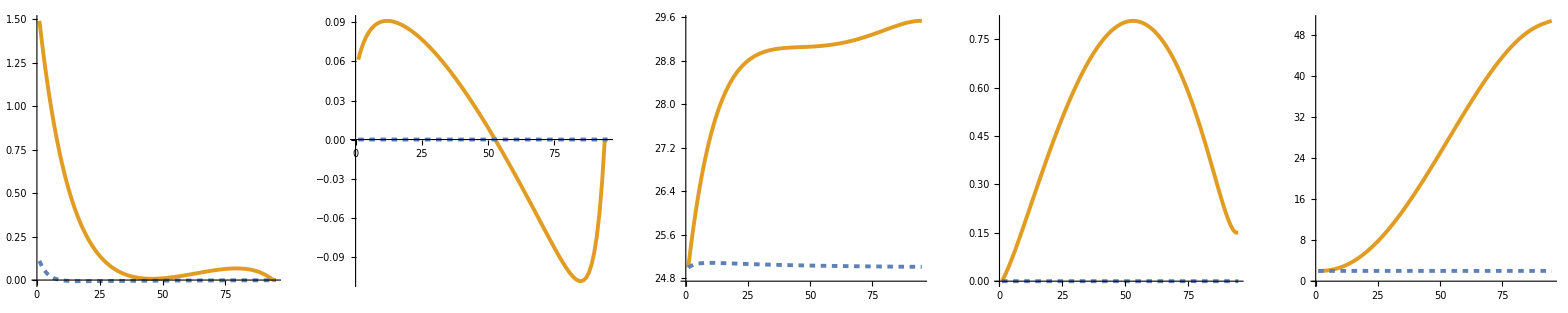

Thread::tdlen: Objects of unequal length in {1.49037,1.36751,1.25399,1.14914,1.05232,0.96292,0.880374,0.804232,0.733965,0.66919,«85»}+{-0.11,-0.079,-0.0556,-0.0383,-0.0255,-0.0162,-0.0094,-0.0045,-0.001,0.0015,«87»} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.0613931,0.0686597,0.0744163,0.0789589,0.0825192,0.0852791,0.0873816,0.088939,0.0900405,0.0907568,«85»}+{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«87»} cannot be combined.

Iteration 2

General::munfl: Exp[-2078.77] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2018.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2028.84] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.1399
1.05328
0.973235
0.899275
0.830936
0.76779
0.709442
0.655529
0.605712
0.559682
0.517149
0.477849
0.441535
0.407981
0.376976
0.348328
0.321857
0.297397
0.274796
0.253913
0.234616
0.216786
0.200311
0.185087
0.171021
0.158023
0.146013
0.134916
0.124662
0.115187
0.106432
0.0983419
0.0908666
0.0839593
0.0775767
0.0716789
0.0662292
0.0611933
0.05654
0.05224
0.0482665
0.0445947
0.0412016
0.038066
0.0351683
0.0324904
0.0300156
0.0277284
0.0256145
0.0236606
0.0218547
0.0201853
0.0186422
0.0172155
0.0158964
0.0146766
0.0135486
0.0125053
0.0115402
0.0106471
0.00982061
0.00905549
0.00834697
0.00769062
0.00708233
0.00651831
0.00599503
0.00550922
0.00505784
0.00463807
0.00424729
0.00388305
0.00354308
0.00322526
0.0029276
0.00264823
0.00238541
0.00213751
0.00190296
0.00168031
0.00146816
0.00126518
0.00107011
0.00088173
0.000698861
0.000520359
0.00034511
0.000172017
0.
0.)(uy
-0.215157
-0.292261
-0.104112
0.0727656
0.118903
0.0926616
0.0722116
0.0562748
0.0438552
0.0341766
0.026634
0.020756
0.0161752
0.0126054
0.00982346
0.00765546
0.00596594
0.00464928
0.00362321
0.00282358
0.00220043
0.0017148
0.00133635
0.00104143
0.000811589
0.000632475
0.00049289
0.000384112
0.00029934
0.000233277
0.000181794
0.000141673
0.000110406
0.00008604
0.0000670513
0.0000522534
0.0000407213
0.0000317343
0.0000247307
0.0000192727
0.0000150193
0.0000117046
9.12147×10^-6
7.1084×10^-6
5.53961×10^-6
4.31704×10^-6
3.36429×10^-6
2.62181×10^-6
2.04318×10^-6
1.59226×10^-6
1.24086×10^-6
9.67006×10^-7
7.53592×10^-7
5.87278×10^-7
4.57668×10^-7
3.56663×10^-7
2.77949×10^-7
2.16607×10^-7
1.68803×10^-7
1.31549×10^-7
1.02516×10^-7
7.98915×10^-8
6.22598×10^-8
4.85193×10^-8
3.78113×10^-8
2.94665×10^-8
2.29634×10^-8
1.78954×10^-8
1.3946×10^-8
1.08681×10^-8
8.46955×10^-9
6.60032×10^-9
5.1436×10^-9
4.00836×10^-9
3.12364×10^-9
2.43414×10^-9
1.89678×10^-9
1.47797×10^-9
1.15154×10^-9
8.97069×10^-10
6.9867×10^-10
5.43937×10^-10
4.23201×10^-10
3.28915×10^-10
2.55186×10^-10
1.97406×10^-10
1.51964×10^-10
1.16019×10^-10
8.73261×10^-11
6.40909×10^-11
4.48612×10^-11
2.84354×10^-11
1.37869×10^-11
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.942
195.51
222.338
249.408
276.701
304.199
331.887
359.751
387.777
415.953
444.268
472.711
501.272
529.943
558.715
587.58
616.531
645.562
674.666
703.839
733.074
762.368
791.715
821.112
850.555
880.04
909.564
939.124
968.718
998.343
1028.
1057.68
1087.38
1117.11
1146.85
1176.62
1206.4
1236.2
1266.02
1295.85
1325.69
1355.55
1385.41
1415.29
1445.17
1475.07
1504.97
1534.88
1564.79
1594.72
1624.64
1654.58
1684.52
1714.46
1744.41
1774.36
1804.32
1834.27
1864.24
1894.2
1924.17
1954.14
1984.11
2014.08
2044.06
2074.04
2104.02
2134.
2163.98
2193.96
2223.95
2253.93
2283.92
2313.91
2343.89
2373.88
2403.87
2433.86
2463.85
2493.85
2523.84
2553.83
2583.82
2613.81
2643.81
2673.8
2703.79
2733.78
2763.78)(y
2.
1.99328
1.93035
1.80025
1.64964
1.51866
1.41659
1.33705
1.27506
1.22675
1.18911
1.15977
1.1369
1.11909
1.1052
1.09438
1.08595
1.07938
1.07425
1.07026
1.06715
1.06473
1.06284
1.06137
1.06022
1.05933
1.05863
1.05809
1.05766
1.05733
1.05708
1.05688
1.05672
1.0566
1.0565
1.05643
1.05637
1.05633
1.05629
1.05627
1.05625
1.05623
1.05622
1.05621
1.0562
1.05619
1.05619
1.05618
1.05618
1.05618
1.05618
1.05618
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617
1.05617)(vx
25.
25.25
25.5
25.75
26.
26.25
26.535
26.7983
27.0416
27.2664
27.4742
27.6661
27.8435
28.0073
28.1588
28.2987
28.428
28.5474
28.6578
28.7598
28.8541
28.9411
29.0216
29.096
29.1647
29.2281
29.2868
29.341
29.3911
29.4373
29.4801
29.5196
29.5561
29.5898
29.621
29.6498
29.6764
29.701
29.7237
29.7447
29.7641
29.782
29.7986
29.8139
29.828
29.8411
29.8531
29.8643
29.8746
29.8841
29.8929
29.901
29.9085
29.9154
29.9218
29.9278
29.9332
29.9383
29.9429
29.9472
29.9512
29.9549
29.9583
29.9614
29.9643
29.9669
29.9694
29.9717
29.9737
29.9757
29.9774
29.9791
29.9806
29.9819
29.9832
29.9844
29.9854
29.9864
29.9873
29.9881
29.9888
29.9895
29.9901
29.9906
29.9911
29.9915
29.9919
29.9922
29.9925
29.9927
29.9929
29.993
29.9931
29.9931
29.9931)(vy
0.
-0.0537893
-0.126855
-0.152883
-0.134691
-0.104965
-0.0818001
-0.0637471
-0.0496784
-0.0387146
-0.0301705
-0.023512
-0.018323
-0.0142792
-0.0111278
-0.00867197
-0.00675811
-0.00526662
-0.0041043
-0.0031985
-0.00249261
-0.0019425
-0.0015138
-0.00117971
-0.000919353
-0.000716456
-0.000558337
-0.000435115
-0.000339087
-0.000264252
-0.000205933
-0.000160484
-0.000125066
-0.0000974646
-0.0000759546
-0.0000591917
-0.0000461284
-0.000035948
-0.0000280145
-0.0000218318
-0.0000170136
-0.0000132588
-0.0000103326
-8.05227×10^-6
-6.27517×10^-6
-4.89027×10^-6
-3.81101×10^-6
-2.96993×10^-6
-2.31448×10^-6
-1.80369×10^-6
-1.40562×10^-6
-1.09541×10^-6
-8.53655×10^-7
-6.65258×10^-7
-5.18438×10^-7
-4.04021×10^-7
-3.14855×10^-7
-2.45368×10^-7
-1.91217×10^-7
-1.49016×10^-7
-1.16129×10^-7
-9.04997×10^-8
-7.05268×10^-8
-5.49619×10^-8
-4.2832×10^-8
-3.33792×10^-8
-2.60126×10^-8
-2.02717×10^-8
-1.57979×10^-8
-1.23114×10^-8
-9.59434×10^-9
-7.47695×10^-9
-5.82687×10^-9
-4.54097×10^-9
-3.53888×10^-9
-2.75797×10^-9
-2.14944×10^-9
-1.67524×10^-9
-1.30575×10^-9
-1.01786×10^-9
-7.93597×10^-10
-6.1893×10^-10
-4.82945×10^-10
-3.77145×10^-10
-2.94916×10^-10
-2.3112×10^-10
-1.81768×10^-10
-1.43778×10^-10
-1.14773×10^-10
-9.29412×10^-11
-7.69184×10^-11
-6.57031×10^-11
-5.85943×10^-11
-5.51476×10^-11
-5.51476×10^-11)

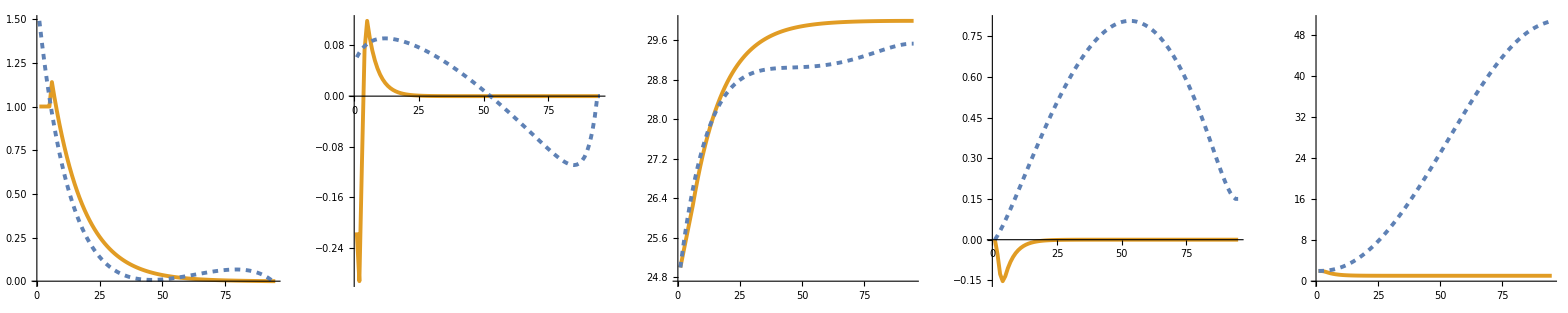

Iteration 3

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.
1.
0.987915
0.91284
0.84347
0.779371
0.720144
0.665417
0.614849
0.568124
0.52495
0.485057
0.448195
0.414135
0.382663
0.353582
0.326712
0.301883
0.278941
0.257743
0.238155
0.220056
0.203332
0.187879
0.173601
0.160407
0.148216
0.136951
0.126542
0.116924
0.108037
0.0998253
0.0922373
0.0852257
0.0787469
0.0727601
0.0672282
0.0621164
0.0573928
0.053028
0.0489946
0.0452674
0.0418231
0.0386402
0.0356988
0.0329805
0.0304684
0.0281466
0.0260008
0.0240175
0.0221844
0.0204898
0.0189234
0.0174751
0.0161362
0.014898
0.013753
0.012694
0.0117142
0.0108077
0.00996875
0.00919209
0.00847288
0.00780663
0.00718917
0.00661664
0.00608546
0.00559232
0.00513413
0.00470803
0.00431135
0.00394162
0.00359653
0.00327391
0.00297176
0.00268818
0.0024214
0.00216975
0.00193167
0.00170565
0.0014903
0.00128426
0.00108625
0.000895031
0.000709403
0.000528208
0.000350316
0.000174612
0.
0.)(uy
-0.0804191
-0.212064
-0.0972692
0.0228829
0.0809665
0.0630976
0.0491722
0.0383201
0.029863
0.0232724
0.0181363
0.0141337
0.0110144
0.00858361
0.00668924
0.00521296
0.00406248
0.00316591
0.00246721
0.00192271
0.00149837
0.00116769
0.000909985
0.000709155
0.000552648
0.000430681
0.000335632
0.000261559
0.000203834
0.000158849
0.000123792
0.0000964714
0.0000751806
0.0000585886
0.0000456583
0.0000355817
0.000027729
0.0000216093
0.0000168403
0.0000131237
0.0000102273
7.97022×10^-6
6.21122×10^-6
4.84044×10^-6
3.77217×10^-6
2.93967×10^-6
2.2909×10^-6
1.78531×10^-6
1.3913×10^-6
1.08424×10^-6
8.44957×10^-7
6.58479×10^-7
5.13155×10^-7
3.99904×10^-7
3.11647×10^-7
2.42868×10^-7
1.89268×10^-7
1.47497×10^-7
1.14945×10^-7
8.95775×10^-8
6.98081×10^-8
5.44018×10^-8
4.23955×10^-8
3.3039×10^-8
2.57475×10^-8
2.00651×10^-8
1.56368×10^-8
1.21858×10^-8
9.49646×10^-9
7.40061×10^-9
5.76731×10^-9
4.49446×10^-9
3.50251×10^-9
2.72947×10^-9
2.12703×10^-9
1.65752×10^-9
1.29161×10^-9
1.00642×10^-9
7.84133×10^-10
6.10855×10^-10
4.75756×10^-10
3.70392×10^-10
2.88177×10^-10
2.23973×10^-10
1.73768×10^-10
1.34423×10^-10
1.03479×10^-10
7.90029×10^-11
5.94644×10^-11
4.36424×10^-11
3.05481×10^-11
1.9363×10^-11
9.38812×10^-12
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.938
195.469
222.25
249.275
276.527
303.987
331.64
359.472
387.469
415.617
443.907
472.326
500.866
529.516
558.269
587.117
616.053
645.069
674.16
703.32
732.544
761.827
791.164
820.552
849.986
879.464
908.981
938.534
968.122
997.741
1027.39
1057.06
1086.76
1116.49
1146.23
1175.99
1205.77
1235.57
1265.38
1295.21
1325.05
1354.9
1384.77
1414.64
1444.52
1474.42
1504.32
1534.22
1564.14
1594.06
1623.99
1653.92
1683.86
1713.8
1743.75
1773.7
1803.65
1833.61
1863.57
1893.54
1923.5
1953.47
1983.44
2013.42
2043.39
2073.37
2103.35
2133.33
2163.31
2193.29
2223.28
2253.26
2283.25
2313.24
2343.23
2373.21
2403.2
2433.19
2463.18
2493.18
2523.17
2553.16
2583.15
2613.14
2643.14
2673.13
2703.12
2733.11
2763.11)(y
2.
1.99749
1.97076
1.89459
1.79787
1.70868
1.63918
1.58502
1.5428
1.50991
1.48427
1.4643
1.44873
1.4366
1.42714
1.41977
1.41403
1.40955
1.40607
1.40335
1.40123
1.39958
1.39829
1.39729
1.39651
1.3959
1.39543
1.39506
1.39477
1.39455
1.39437
1.39423
1.39413
1.39405
1.39398
1.39393
1.39389
1.39386
1.39384
1.39382
1.3938
1.39379
1.39378
1.39378
1.39377
1.39377
1.39376
1.39376
1.39376
1.39376
1.39376
1.39376
1.39376
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375
1.39375)(vx
25.
25.25
25.5
25.75
26.
26.25
26.5
26.75
26.997
27.2252
27.4361
27.6309
27.8109
27.9773
28.131
28.273
28.4043
28.5255
28.6376
28.7411
28.8368
28.9252
29.0069
29.0823
29.1521
29.2165
29.276
29.3311
29.3819
29.4289
29.4723
29.5124
29.5494
29.5836
29.6153
29.6445
29.6715
29.6965
29.7195
29.7408
29.7605
29.7787
29.7955
29.8111
29.8254
29.8387
29.8509
29.8622
29.8727
29.8823
29.8913
29.8995
29.9071
29.9142
29.9207
29.9267
29.9322
29.9373
29.9421
29.9464
29.9505
29.9542
29.9576
29.9608
29.9637
29.9664
29.9689
29.9712
29.9733
29.9753
29.9771
29.9788
29.9803
29.9817
29.983
29.9841
29.9852
29.9862
29.9871
29.9879
29.9887
29.9893
29.9899
29.9905
29.991
29.9914
29.9918
29.9921
29.9924
29.9926
29.9928
29.9929
29.993
29.993
29.993)(vy
0.
-0.0201048
-0.0731208
-0.0974381
-0.0917174
-0.0714758
-0.0557014
-0.0434084
-0.0338283
-0.0263626
-0.0205445
-0.0160104
-0.012477
-0.00972336
-0.00757746
-0.00590514
-0.00460191
-0.00358629
-0.00279481
-0.00217801
-0.00169733
-0.00132274
-0.00103081
-0.000803318
-0.00062603
-0.000487868
-0.000380197
-0.00029629
-0.0002309
-0.000179941
-0.000140229
-0.000109281
-0.0000851632
-0.0000663681
-0.0000517209
-0.0000403064
-0.0000314109
-0.0000244787
-0.0000190763
-0.0000148663
-0.0000115854
-9.02852×10^-6
-7.03596×10^-6
-5.48316×10^-6
-4.27305×10^-6
-3.33001×10^-6
-2.59509×10^-6
-2.02236×10^-6
-1.57604×10^-6
-1.22821×10^-6
-9.57152×10^-7
-7.45913×10^-7
-5.81293×10^-7
-4.53004×10^-7
-3.53028×10^-7
-2.75117×10^-7
-2.144×10^-7
-1.67083×10^-7
-1.30208×10^-7
-1.01472×10^-7
-7.90774×10^-8
-6.16254×10^-8
-4.80249×10^-8
-3.74261×10^-8
-2.91663×10^-8
-2.27294×10^-8
-1.77132×10^-8
-1.38039×10^-8
-1.07575×10^-8
-8.38338×10^-9
-6.53322×10^-9
-5.0914×10^-9
-3.96778×10^-9
-3.09215×10^-9
-2.40979×10^-9
-1.87803×10^-9
-1.46365×10^-9
-1.14075×10^-9
-8.89144×10^-10
-6.93111×10^-10
-5.40397×10^-10
-4.21458×10^-10
-3.2886×10^-10
-2.56815×10^-10
-2.00822×10^-10
-1.5738×10^-10
-1.23774×10^-10
-9.79047×10^-11
-7.8154×10^-11
-6.32879×10^-11
-5.23773×10^-11
-4.47403×10^-11
-3.98995×10^-11
-3.75525×10^-11
-3.75525×10^-11)

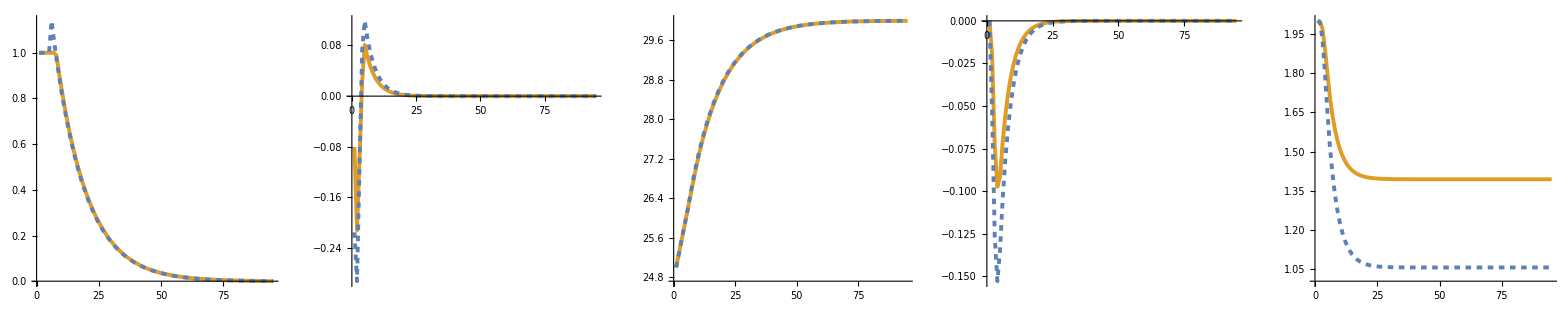

Iteration 4

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.
1.
0.987915
0.91284
0.84347
0.779371
0.720144
0.665417
0.614849
0.568124
0.52495
0.485057
0.448195
0.414135
0.382663
0.353582
0.326712
0.301883
0.278941
0.257743
0.238155
0.220056
0.203332
0.187879
0.173601
0.160407
0.148216
0.136951
0.126542
0.116924
0.108037
0.0998253
0.0922373
0.0852257
0.0787469
0.0727601
0.0672282
0.0621164
0.0573928
0.053028
0.0489946
0.0452674
0.0418231
0.0386402
0.0356988
0.0329805
0.0304684
0.0281466
0.0260008
0.0240175
0.0221844
0.0204898
0.0189234
0.0174751
0.0161362
0.014898
0.013753
0.012694
0.0117142
0.0108077
0.00996875
0.00919209
0.00847288
0.00780663
0.00718917
0.00661664
0.00608546
0.00559232
0.00513413
0.00470803
0.00431135
0.00394162
0.00359653
0.00327391
0.00297176
0.00268818
0.0024214
0.00216975
0.00193167
0.00170565
0.0014903
0.00128426
0.00108625
0.000895031
0.000709403
0.000528208
0.000350316
0.000174612
0.
0.)(uy
-0.141758
-0.246936
-0.0964761
0.0436969
0.0974311
0.0759285
0.0591714
0.0461126
0.0359357
0.0280049
0.0218243
0.0170078
0.0132542
0.0103291
0.00804951
0.00627302
0.00488859
0.0038097
0.00296892
0.00231369
0.00180307
0.00140514
0.00109503
0.000853363
0.000665029
0.00051826
0.000403883
0.000314747
0.000245284
0.000191151
0.000148965
0.000116089
0.0000904686
0.0000705026
0.000054943
0.0000428173
0.0000333677
0.0000260036
0.0000202647
0.0000157924
0.0000123071
9.59097×10^-6
7.47428×10^-6
5.82474×10^-6
4.53925×10^-6
3.53746×10^-6
2.75675×10^-6
2.14835×10^-6
1.67422×10^-6
1.30473×10^-6
1.01678×10^-6
7.92381×10^-7
6.17506×10^-7
4.81225×10^-7
3.75021×10^-7
2.92255×10^-7
2.27756×10^-7
1.77491×10^-7
1.3832×10^-7
1.07793×10^-7
8.40037×10^-8
6.54644×10^-8
5.10167×10^-8
3.97576×10^-8
3.09832×10^-8
2.41454×10^-8
1.88166×10^-8
1.46638×10^-8
1.14276×10^-8
8.90553×10^-9
6.94009×10^-9
5.40841×10^-9
4.21475×10^-9
3.28451×10^-9
2.55956×10^-9
1.99458×10^-9
1.55426×10^-9
1.21108×10^-9
9.43587×10^-10
7.35074×10^-10
5.72502×10^-10
4.45711×10^-10
3.46778×10^-10
2.69518×10^-10
2.09104×10^-10
1.61758×10^-10
1.24522×10^-10
9.50682×10^-11
7.15565×10^-11
5.25171×10^-11
3.67601×10^-11
2.33005×10^-11
1.12972×10^-11
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.938
195.469
222.25
249.275
276.527
303.987
331.64
359.472
387.469
415.617
443.907
472.326
500.866
529.516
558.269
587.117
616.053
645.069
674.16
703.32
732.544
761.827
791.164
820.552
849.986
879.464
908.981
938.534
968.122
997.741
1027.39
1057.06
1086.76
1116.49
1146.23
1175.99
1205.77
1235.57
1265.38
1295.21
1325.05
1354.9
1384.77
1414.64
1444.52
1474.42
1504.32
1534.22
1564.14
1594.06
1623.99
1653.92
1683.86
1713.8
1743.75
1773.7
1803.65
1833.61
1863.57
1893.54
1923.5
1953.47
1983.44
2013.42
2043.39
2073.37
2103.35
2133.33
2163.31
2193.29
2223.28
2253.26
2283.25
2313.24
2343.23
2373.21
2403.2
2433.19
2463.18
2493.18
2523.17
2553.16
2583.15
2613.14
2643.14
2673.13
2703.12
2733.11
2763.11)(y
2.
1.99557
1.95241
1.85223
1.7323
1.62498
1.54134
1.47616
1.42536
1.38578
1.35493
1.33089
1.31216
1.29756
1.28618
1.27731
1.2704
1.26502
1.26082
1.25755
1.255
1.25302
1.25147
1.25026
1.24932
1.24859
1.24802
1.24757
1.24723
1.24696
1.24675
1.24658
1.24645
1.24635
1.24628
1.24622
1.24617
1.24613
1.2461
1.24608
1.24606
1.24605
1.24604
1.24603
1.24602
1.24602
1.24602
1.24601
1.24601
1.24601
1.24601
1.24601
1.24601
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246
1.246)(vx
25.
25.25
25.5
25.75
26.
26.25
26.5
26.75
26.997
27.2252
27.4361
27.6309
27.8109
27.9773
28.131
28.273
28.4043
28.5255
28.6376
28.7411
28.8368
28.9252
29.0069
29.0823
29.1521
29.2165
29.276
29.3311
29.3819
29.4289
29.4723
29.5124
29.5494
29.5836
29.6153
29.6445
29.6715
29.6965
29.7195
29.7408
29.7605
29.7787
29.7955
29.8111
29.8254
29.8387
29.8509
29.8622
29.8727
29.8823
29.8913
29.8995
29.9071
29.9142
29.9207
29.9267
29.9322
29.9373
29.9421
29.9464
29.9505
29.9542
29.9576
29.9608
29.9637
29.9664
29.9689
29.9712
29.9733
29.9753
29.9771
29.9788
29.9803
29.9817
29.983
29.9841
29.9852
29.9862
29.9871
29.9879
29.9887
29.9893
29.9899
29.9905
29.991
29.9914
29.9918
29.9921
29.9924
29.9926
29.9928
29.9929
29.993
29.993
29.993)(vy
0.
-0.0354394
-0.0971734
-0.121292
-0.110368
-0.0860105
-0.0670283
-0.0522355
-0.0407073
-0.0317234
-0.0247222
-0.0192661
-0.0150142
-0.0117006
-0.00911834
-0.00710596
-0.00553771
-0.00431556
-0.00336313
-0.00262091
-0.00204248
-0.00159172
-0.00124043
-0.000966674
-0.000753333
-0.000587076
-0.000457511
-0.00035654
-0.000277853
-0.000216532
-0.000168745
-0.000131503
-0.000102481
-0.0000798641
-0.0000622384
-0.0000485027
-0.0000377984
-0.0000294564
-0.0000229555
-0.0000178893
-0.0000139412
-0.0000108645
-8.46674×10^-6
-6.59816×10^-6
-5.14198×10^-6
-4.00717×10^-6
-3.1228×10^-6
-2.43361×10^-6
-1.89653×10^-6
-1.47797×10^-6
-1.15179×10^-6
-8.97595×10^-7
-6.995×10^-7
-5.45123×10^-7
-4.24817×10^-7
-3.31062×10^-7
-2.57998×10^-7
-2.01059×10^-7
-1.56686×10^-7
-1.22106×10^-7
-9.51579×10^-8
-7.4157×10^-8
-5.77909×10^-8
-4.50367×10^-8
-3.50973×10^-8
-2.73515×10^-8
-2.13151×10^-8
-1.6611×10^-8
-1.2945×10^-8
-1.00881×10^-8
-7.86176×10^-9
-6.12674×10^-9
-4.77463×10^-9
-3.72095×10^-9
-2.89982×10^-9
-2.25993×10^-9
-1.76128×10^-9
-1.37272×10^-9
-1.06995×10^-9
-8.34055×10^-10
-6.50287×10^-10
-5.07161×10^-10
-3.95734×10^-10
-3.09039×10^-10
-2.41659×10^-10
-1.89384×10^-10
-1.48944×10^-10
-1.17814×10^-10
-9.40467×10^-11
-7.61575×10^-11
-6.30283×10^-11
-5.38383×10^-11
-4.80131×10^-11
-4.51888×10^-11
-4.51888×10^-11)

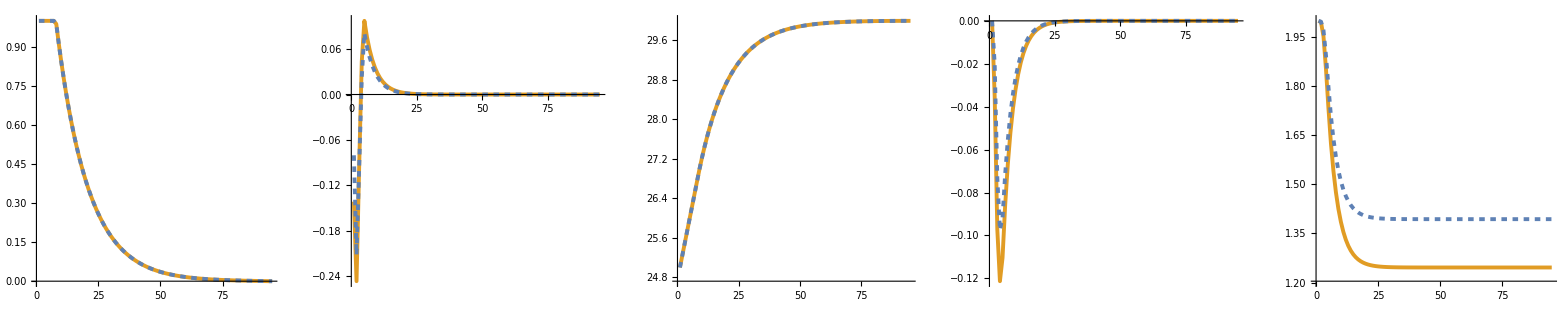

Iteration 5

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.
1.
0.987915
0.91284
0.84347
0.779371
0.720144
0.665417
0.614849
0.568124
0.52495
0.485057
0.448195
0.414135
0.382663
0.353582
0.326712
0.301883
0.278941
0.257743
0.238155
0.220056
0.203332
0.187879
0.173601
0.160407
0.148216
0.136951
0.126542
0.116924
0.108037
0.0998253
0.0922373
0.0852257
0.0787469
0.0727601
0.0672282
0.0621164
0.0573928
0.053028
0.0489946
0.0452674
0.0418231
0.0386402
0.0356988
0.0329805
0.0304684
0.0281466
0.0260008
0.0240175
0.0221844
0.0204898
0.0189234
0.0174751
0.0161362
0.014898
0.013753
0.012694
0.0117142
0.0108077
0.00996875
0.00919209
0.00847288
0.00780663
0.00718917
0.00661664
0.00608546
0.00559232
0.00513413
0.00470803
0.00431135
0.00394162
0.00359653
0.00327391
0.00297176
0.00268818
0.0024214
0.00216975
0.00193167
0.00170565
0.0014903
0.00128426
0.00108625
0.000895031
0.000709403
0.000528208
0.000350316
0.000174612
0.
0.)(uy
-0.113963
-0.231132
-0.097797
0.0335904
0.090331
0.0703954
0.0548594
0.0427522
0.033317
0.0259641
0.0202339
0.0157684
0.0122884
0.00957638
0.00746292
0.00581588
0.00453234
0.00353208
0.00275256
0.00214508
0.00167167
0.00130274
0.00101523
0.000791176
0.000616567
0.000480493
0.000374451
0.000291811
0.00022741
0.000177221
0.000138109
0.000107629
0.0000838759
0.0000653649
0.0000509391
0.0000396971
0.0000309361
0.0000241087
0.000018788
0.0000146416
0.0000114102
8.89205×10^-6
6.92961×10^-6
5.40028×10^-6
4.20846×10^-6
3.27967×10^-6
2.55586×10^-6
1.9918×10^-6
1.55221×10^-6
1.20965×10^-6
9.42684×10^-7
7.34638×10^-7
5.72507×10^-7
4.46157×10^-7
3.47692×10^-7
2.70958×10^-7
2.11159×10^-7
1.64557×10^-7
1.2824×10^-7
9.9938×10^-8
7.78821×10^-8
6.06939×10^-8
4.7299×10^-8
3.68603×10^-8
2.87254×10^-8
2.23858×10^-8
1.74454×10^-8
1.35952×10^-8
1.05948×10^-8
8.25656×10^-9
6.43435×10^-9
5.01428×10^-9
3.90761×10^-9
3.04516×10^-9
2.37304×10^-9
1.84923×10^-9
1.44099×10^-9
1.12282×10^-9
8.74826×10^-10
6.81507×10^-10
5.30782×10^-10
4.13231×10^-10
3.21507×10^-10
2.49878×10^-10
1.93866×10^-10
1.4997×10^-10
1.15447×10^-10
8.81403×10^-11
6.6342×10^-11
4.86901×10^-11
3.40812×10^-11
2.16025×10^-11
1.04739×10^-11
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.938
195.469
222.25
249.275
276.527
303.987
331.64
359.472
387.469
415.617
443.907
472.326
500.866
529.516
558.269
587.117
616.053
645.069
674.16
703.32
732.544
761.827
791.164
820.552
849.986
879.464
908.981
938.534
968.122
997.741
1027.39
1057.06
1086.76
1116.49
1146.23
1175.99
1205.77
1235.57
1265.38
1295.21
1325.05
1354.9
1384.77
1414.64
1444.52
1474.42
1504.32
1534.22
1564.14
1594.06
1623.99
1653.92
1683.86
1713.8
1743.75
1773.7
1803.65
1833.61
1863.57
1893.54
1923.5
1953.47
1983.44
2013.42
2043.39
2073.37
2103.35
2133.33
2163.31
2193.29
2223.28
2253.26
2283.25
2313.24
2343.23
2373.21
2403.2
2433.19
2463.18
2493.18
2523.17
2553.16
2583.15
2613.14
2643.14
2673.13
2703.12
2733.11
2763.11)(y
2.
1.99644
1.96073
1.8714
1.76172
1.66222
1.58468
1.52425
1.47715
1.44045
1.41185
1.38957
1.3722
1.35866
1.34811
1.33989
1.33348
1.32849
1.3246
1.32157
1.31921
1.31737
1.31593
1.31481
1.31394
1.31326
1.31273
1.31232
1.312
1.31175
1.31155
1.3114
1.31128
1.31119
1.31112
1.31106
1.31102
1.31098
1.31096
1.31094
1.31092
1.31091
1.3109
1.31089
1.31088
1.31088
1.31088
1.31087
1.31087
1.31087
1.31087
1.31087
1.31087
1.31087
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086
1.31086)(vx
25.
25.25
25.5
25.75
26.
26.25
26.5
26.75
26.997
27.2252
27.4361
27.6309
27.8109
27.9773
28.131
28.273
28.4043
28.5255
28.6376
28.7411
28.8368
28.9252
29.0069
29.0823
29.1521
29.2165
29.276
29.3311
29.3819
29.4289
29.4723
29.5124
29.5494
29.5836
29.6153
29.6445
29.6715
29.6965
29.7195
29.7408
29.7605
29.7787
29.7955
29.8111
29.8254
29.8387
29.8509
29.8622
29.8727
29.8823
29.8913
29.8995
29.9071
29.9142
29.9207
29.9267
29.9322
29.9373
29.9421
29.9464
29.9505
29.9542
29.9576
29.9608
29.9637
29.9664
29.9689
29.9712
29.9733
29.9753
29.9771
29.9788
29.9803
29.9817
29.983
29.9841
29.9852
29.9862
29.9871
29.9879
29.9887
29.9893
29.9899
29.9905
29.991
29.9914
29.9918
29.9921
29.9924
29.9926
29.9928
29.9929
29.993
29.993
29.993)(vy
0.
-0.0284907
-0.0862738
-0.110723
-0.102325
-0.0797426
-0.0621438
-0.0484289
-0.0377409
-0.0294116
-0.0229206
-0.0178621
-0.01392
-0.010848
-0.00845386
-0.00658813
-0.00513416
-0.00400107
-0.00311805
-0.00242991
-0.00189364
-0.00147572
-0.00115004
-0.00089623
-0.000698436
-0.000544294
-0.000424171
-0.000330558
-0.000257606
-0.000200753
-0.000156448
-0.00012192
-0.0000950132
-0.0000740442
-0.000057703
-0.0000449682
-0.0000350439
-0.0000273099
-0.0000212827
-0.0000165857
-0.0000129253
-0.0000100728
-7.84974×10^-6
-6.11734×10^-6
-4.76727×10^-6
-3.71515×10^-6
-2.89524×10^-6
-2.25627×10^-6
-1.75832×10^-6
-1.37027×10^-6
-1.06786×10^-6
-8.32185×10^-7
-6.48525×10^-7
-5.05399×10^-7
-3.93859×10^-7
-3.06936×10^-7
-2.39197×10^-7
-1.86407×10^-7
-1.45268×10^-7
-1.13208×10^-7
-8.82235×10^-8
-6.87529×10^-8
-5.35795×10^-8
-4.17547×10^-8
-3.25396×10^-8
-2.53583×10^-8
-1.97618×10^-8
-1.54005×10^-8
-1.20017×10^-8
-9.35299×10^-9
-7.28885×10^-9
-5.68026×10^-9
-4.42669×10^-9
-3.44979×10^-9
-2.6885×10^-9
-2.09524×10^-9
-1.63294×10^-9
-1.27269×10^-9
-9.91982×10^-10
-7.73275×10^-10
-6.02899×10^-10
-4.70203×10^-10
-3.66895×10^-10
-2.86518×10^-10
-2.24049×10^-10
-1.75583×10^-10
-1.3809×10^-10
-1.09228×10^-10
-8.71932×10^-11
-7.06077×10^-11
-5.84352×10^-11
-4.99149×10^-11
-4.45143×10^-11
-4.18958×10^-11
-4.18958×10^-11)

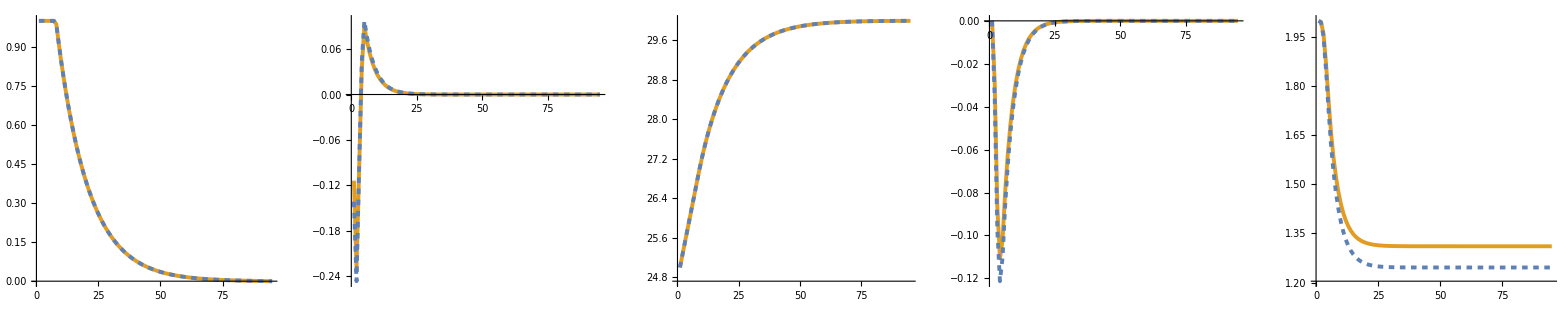

Iteration 6

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.
1.
0.987915
0.91284
0.84347
0.779371
0.720144
0.665417
0.614849
0.568124
0.52495
0.485057
0.448195
0.414135
0.382663
0.353582
0.326712
0.301883
0.278941
0.257743
0.238155
0.220056
0.203332
0.187879
0.173601
0.160407
0.148216
0.136951
0.126542
0.116924
0.108037
0.0998253
0.0922373
0.0852257
0.0787469
0.0727601
0.0672282
0.0621164
0.0573928
0.053028
0.0489946
0.0452674
0.0418231
0.0386402
0.0356988
0.0329805
0.0304684
0.0281466
0.0260008
0.0240175
0.0221844
0.0204898
0.0189234
0.0174751
0.0161362
0.014898
0.013753
0.012694
0.0117142
0.0108077
0.00996875
0.00919209
0.00847288
0.00780663
0.00718917
0.00661664
0.00608546
0.00559232
0.00513413
0.00470803
0.00431135
0.00394162
0.00359653
0.00327391
0.00297176
0.00268818
0.0024214
0.00216975
0.00193167
0.00170565
0.0014903
0.00128426
0.00108625
0.000895031
0.000709403
0.000528208
0.000350316
0.000174612
0.
0.)(uy
-0.12634
-0.238169
-0.0973843
0.0379607
0.09356
0.0729117
0.0568204
0.0442804
0.0345079
0.0268922
0.0209572
0.016332
0.0127276
0.0099187
0.00772969
0.00602378
0.00469436
0.00365833
0.00285096
0.00222176
0.00173143
0.00134931
0.00105152
0.000819457
0.000638607
0.000497669
0.000387836
0.000302242
0.000235539
0.000183556
0.000143046
0.000111477
0.0000868742
0.0000677014
0.00005276
0.0000411161
0.000032042
0.0000249705
0.0000194596
0.0000151649
0.0000118181
9.2099×10^-6
7.17732×10^-6
5.59332×10^-6
4.3589×10^-6
3.39691×10^-6
2.64722×10^-6
2.06299×10^-6
1.6077×10^-6
1.25289×10^-6
9.76381×10^-7
7.60898×10^-7
5.92971×10^-7
4.62105×10^-7
3.60121×10^-7
2.80644×10^-7
2.18707×10^-7
1.70439×10^-7
1.32824×10^-7
1.0351×10^-7
8.06661×10^-8
6.28634×10^-8
4.89897×10^-8
3.81779×10^-8
2.97522×10^-8
2.3186×10^-8
1.8069×10^-8
1.40812×10^-8
1.09735×10^-8
8.5517×10^-9
6.66435×10^-9
5.19352×10^-9
4.04729×10^-9
3.15401×10^-9
2.45786×10^-9
1.91533×10^-9
1.4925×10^-9
1.16296×10^-9
9.06097×10^-10
7.05868×10^-10
5.49755×10^-10
4.28003×10^-10
3.33×10^-10
2.5881×10^-10
2.00795×10^-10
1.55331×10^-10
1.19574×10^-10
9.1291×10^-11
6.87134×10^-11
5.04305×10^-11
3.52995×10^-11
2.23747×10^-11
1.08483×10^-11
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.938
195.469
222.25
249.275
276.527
303.987
331.64
359.472
387.469
415.617
443.907
472.326
500.866
529.516
558.269
587.117
616.053
645.069
674.16
703.32
732.544
761.827
791.164
820.552
849.986
879.464
908.981
938.534
968.122
997.741
1027.39
1057.06
1086.76
1116.49
1146.23
1175.99
1205.77
1235.57
1265.38
1295.21
1325.05
1354.9
1384.77
1414.64
1444.52
1474.42
1504.32
1534.22
1564.14
1594.06
1623.99
1653.92
1683.86
1713.8
1743.75
1773.7
1803.65
1833.61
1863.57
1893.54
1923.5
1953.47
1983.44
2013.42
2043.39
2073.37
2103.35
2133.33
2163.31
2193.29
2223.28
2253.26
2283.25
2313.24
2343.23
2373.21
2403.2
2433.19
2463.18
2493.18
2523.17
2553.16
2583.15
2613.14
2643.14
2673.13
2703.12
2733.11
2763.11)(y
2.
1.99605
1.95702
1.86285
1.74857
1.64551
1.56519
1.5026
1.45383
1.41582
1.38619
1.36311
1.34512
1.3311
1.32017
1.31166
1.30502
1.29985
1.29582
1.29268
1.29023
1.28833
1.28684
1.28568
1.28478
1.28408
1.28353
1.2831
1.28277
1.28251
1.28231
1.28215
1.28202
1.28193
1.28185
1.2818
1.28175
1.28172
1.28169
1.28167
1.28165
1.28164
1.28163
1.28162
1.28161
1.28161
1.2816
1.2816
1.2816
1.2816
1.2816
1.2816
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159
1.28159)(vx
25.
25.25
25.5
25.75
26.
26.25
26.5
26.75
26.997
27.2252
27.4361
27.6309
27.8109
27.9773
28.131
28.273
28.4043
28.5255
28.6376
28.7411
28.8368
28.9252
29.0069
29.0823
29.1521
29.2165
29.276
29.3311
29.3819
29.4289
29.4723
29.5124
29.5494
29.5836
29.6153
29.6445
29.6715
29.6965
29.7195
29.7408
29.7605
29.7787
29.7955
29.8111
29.8254
29.8387
29.8509
29.8622
29.8727
29.8823
29.8913
29.8995
29.9071
29.9142
29.9207
29.9267
29.9322
29.9373
29.9421
29.9464
29.9505
29.9542
29.9576
29.9608
29.9637
29.9664
29.9689
29.9712
29.9733
29.9753
29.9771
29.9788
29.9803
29.9817
29.983
29.9841
29.9852
29.9862
29.9871
29.9879
29.9887
29.9893
29.9899
29.9905
29.991
29.9914
29.9918
29.9921
29.9924
29.9926
29.9928
29.9929
29.993
29.993
29.993)(vy
0.
-0.0315849
-0.0911272
-0.115473
-0.105983
-0.0825931
-0.0643652
-0.0501601
-0.03909
-0.030463
-0.0237399
-0.0185006
-0.0144176
-0.0112357
-0.00875605
-0.00682363
-0.00531768
-0.0041441
-0.00322951
-0.00251677
-0.00196133
-0.00152848
-0.00119115
-0.000928266
-0.000723402
-0.000563751
-0.000439333
-0.000342374
-0.000266814
-0.000207929
-0.00016204
-0.000126279
-0.0000984095
-0.000076691
-0.0000597656
-0.0000465756
-0.0000362966
-0.0000282861
-0.0000220435
-0.0000171786
-0.0000133873
-0.0000104328
-8.13034×10^-6
-6.33601×10^-6
-4.93768×10^-6
-3.84796×10^-6
-2.99873×10^-6
-2.33692×10^-6
-1.82117×10^-6
-1.41925×10^-6
-1.10603×10^-6
-8.61932×10^-7
-6.71707×10^-7
-5.23465×10^-7
-4.07938×10^-7
-3.17908×10^-7
-2.47747×10^-7
-1.9307×10^-7
-1.50461×10^-7
-1.17255×10^-7
-9.13771×10^-8
-7.12106×10^-8
-5.54947×10^-8
-4.32473×10^-8
-3.37028×10^-8
-2.62648×10^-8
-2.04683×10^-8
-1.5951×10^-8
-1.24307×10^-8
-9.68732×10^-9
-7.5494×10^-9
-5.88331×10^-9
-4.58493×10^-9
-3.57311×10^-9
-2.7846×10^-9
-2.17014×10^-9
-1.69131×10^-9
-1.31818×10^-9
-1.02744×10^-9
-8.00917×10^-10
-6.2445×10^-10
-4.87011×10^-10
-3.8001×10^-10
-2.9676×10^-10
-2.32058×10^-10
-1.81859×10^-10
-1.43026×10^-10
-1.13133×10^-10
-9.031×10^-11
-7.31317×10^-11
-6.0524×10^-11
-5.16992×10^-11
-4.61055×10^-11
-4.33934×10^-11
-4.33934×10^-11)

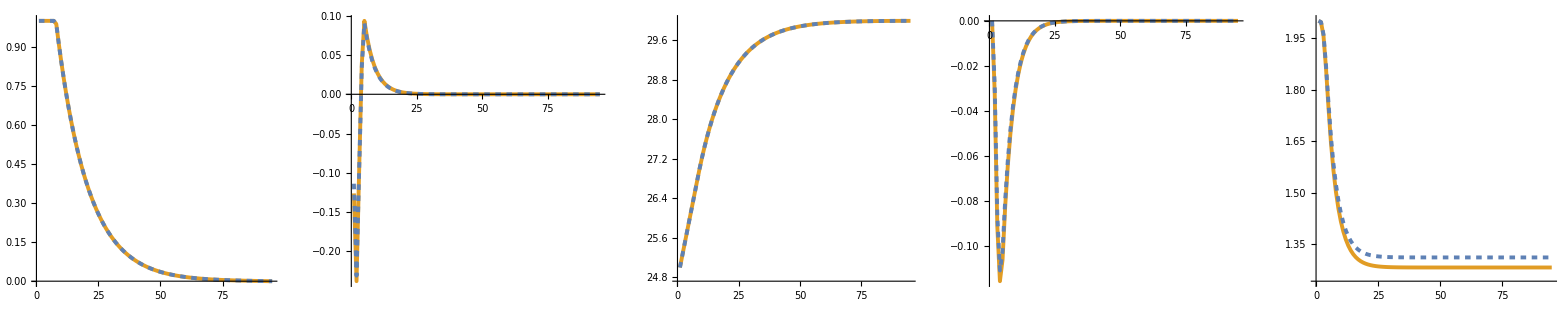

Iteration 7

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.
1.
0.987915
0.91284
0.84347
0.779371
0.720144
0.665417
0.614849
0.568124
0.52495
0.485057
0.448195
0.414135
0.382663
0.353582
0.326712
0.301883
0.278941
0.257743
0.238155
0.220056
0.203332
0.187879
0.173601
0.160407
0.148216
0.136951
0.126542
0.116924
0.108037
0.0998253
0.0922373
0.0852257
0.0787469
0.0727601
0.0672282
0.0621164
0.0573928
0.053028
0.0489946
0.0452674
0.0418231
0.0386402
0.0356988
0.0329805
0.0304684
0.0281466
0.0260008
0.0240175
0.0221844
0.0204898
0.0189234
0.0174751
0.0161362
0.014898
0.013753
0.012694
0.0117142
0.0108077
0.00996875
0.00919209
0.00847288
0.00780663
0.00718917
0.00661664
0.00608546
0.00559232
0.00513413
0.00470803
0.00431135
0.00394162
0.00359653
0.00327391
0.00297176
0.00268818
0.0024214
0.00216975
0.00193167
0.00170565
0.0014903
0.00128426
0.00108625
0.000895031
0.000709403
0.000528208
0.000350316
0.000174612
0.
0.)(uy
-0.120785
-0.235011
-0.0976034
0.0359742
0.0921238
0.0717925
0.0559482
0.0436007
0.0339782
0.0264794
0.0206355
0.0160813
0.0125323
0.00976644
0.00761103
0.00593131
0.0046223
0.00360218
0.00280719
0.00218766
0.00170485
0.0013286
0.00103538
0.000806878
0.000628804
0.000490029
0.000381882
0.000297602
0.000231923
0.000180739
0.00014085
0.000109765
0.0000855406
0.0000666622
0.0000519501
0.000040485
0.0000315501
0.0000245871
0.0000191609
0.0000149321
0.0000116367
9.06852×10^-6
7.06714×10^-6
5.50745×10^-6
4.29198×10^-6
3.34476×10^-6
2.60659×10^-6
2.03133×10^-6
1.58302×10^-6
1.23366×10^-6
9.61393×10^-7
7.49218×10^-7
5.83869×10^-7
4.55012×10^-7
3.54593×10^-7
2.76336×10^-7
2.1535×10^-7
1.67823×10^-7
1.30785×10^-7
1.01921×10^-7
7.94278×10^-8
6.18984×10^-8
4.82377×10^-8
3.75919×10^-8
2.92955×10^-8
2.28301×10^-8
1.77916×10^-8
1.38651×10^-8
1.08051×10^-8
8.42043×10^-9
6.56205×10^-9
5.1138×10^-9
3.98516×10^-9
3.1056×10^-9
2.42013×10^-9
1.88593×10^-9
1.46959×10^-9
1.14511×10^-9
8.92188×10^-10
6.95032×10^-10
5.41316×10^-10
4.21432×10^-10
3.27888×10^-10
2.54837×10^-10
1.97713×10^-10
1.52946×10^-10
1.17739×10^-10
8.98896×10^-11
6.76586×10^-11
4.96564×10^-11
3.47576×10^-11
2.20313×10^-11
1.06818×10^-11
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.938
195.469
222.25
249.275
276.527
303.987
331.64
359.472
387.469
415.617
443.907
472.326
500.866
529.516
558.269
587.117
616.053
645.069
674.16
703.32
732.544
761.827
791.164
820.552
849.986
879.464
908.981
938.534
968.122
997.741
1027.39
1057.06
1086.76
1116.49
1146.23
1175.99
1205.77
1235.57
1265.38
1295.21
1325.05
1354.9
1384.77
1414.64
1444.52
1474.42
1504.32
1534.22
1564.14
1594.06
1623.99
1653.92
1683.86
1713.8
1743.75
1773.7
1803.65
1833.61
1863.57
1893.54
1923.5
1953.47
1983.44
2013.42
2043.39
2073.37
2103.35
2133.33
2163.31
2193.29
2223.28
2253.26
2283.25
2313.24
2343.23
2373.21
2403.2
2433.19
2463.18
2493.18
2523.17
2553.16
2583.15
2613.14
2643.14
2673.13
2703.12
2733.11
2763.11)(y
2.
1.99623
1.95869
1.86669
1.75446
1.65298
1.5739
1.51227
1.46425
1.42682
1.39765
1.37492
1.3572
1.3434
1.33264
1.32426
1.31772
1.31263
1.30866
1.30557
1.30316
1.30128
1.29982
1.29868
1.29779
1.2971
1.29656
1.29614
1.29581
1.29556
1.29536
1.2952
1.29508
1.29499
1.29491
1.29486
1.29481
1.29478
1.29475
1.29473
1.29471
1.2947
1.29469
1.29468
1.29468
1.29467
1.29467
1.29466
1.29466
1.29466
1.29466
1.29466
1.29466
1.29466
1.29466
1.29466
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465
1.29465)(vx
25.
25.25
25.5
25.75
26.
26.25
26.5
26.75
26.997
27.2252
27.4361
27.6309
27.8109
27.9773
28.131
28.273
28.4043
28.5255
28.6376
28.7411
28.8368
28.9252
29.0069
29.0823
29.1521
29.2165
29.276
29.3311
29.3819
29.4289
29.4723
29.5124
29.5494
29.5836
29.6153
29.6445
29.6715
29.6965
29.7195
29.7408
29.7605
29.7787
29.7955
29.8111
29.8254
29.8387
29.8509
29.8622
29.8727
29.8823
29.8913
29.8995
29.9071
29.9142
29.9207
29.9267
29.9322
29.9373
29.9421
29.9464
29.9505
29.9542
29.9576
29.9608
29.9637
29.9664
29.9689
29.9712
29.9733
29.9753
29.9771
29.9788
29.9803
29.9817
29.983
29.9841
29.9852
29.9862
29.9871
29.9879
29.9887
29.9893
29.9899
29.9905
29.991
29.9914
29.9918
29.9921
29.9924
29.9926
29.9928
29.9929
29.993
29.993
29.993)(vy
0.
-0.0301962
-0.0889489
-0.11335
-0.104356
-0.0813253
-0.0633771
-0.0493901
-0.0384899
-0.0299954
-0.0233755
-0.0182166
-0.0141963
-0.0110632
-0.00862164
-0.00671888
-0.00523605
-0.00408048
-0.00317994
-0.00247814
-0.00193122
-0.00150501
-0.00117286
-0.000914017
-0.000712297
-0.000555097
-0.000432589
-0.000337119
-0.000262718
-0.000204737
-0.000159553
-0.00012434
-0.0000968988
-0.0000755137
-0.0000588482
-0.0000458606
-0.0000357394
-0.0000278519
-0.0000217051
-0.0000169149
-0.0000131818
-0.0000102727
-8.00553×10^-6
-6.23875×10^-6
-4.86188×10^-6
-3.78889×10^-6
-2.9527×10^-6
-2.30105×10^-6
-1.79322×10^-6
-1.39746×10^-6
-1.08905×10^-6
-8.48701×10^-7
-6.61396×10^-7
-5.15429×10^-7
-4.01676×10^-7
-3.13028×10^-7
-2.43944×10^-7
-1.90107×10^-7
-1.48151×10^-7
-1.15455×10^-7
-8.99744×10^-8
-7.01174×10^-8
-5.46428×10^-8
-4.25834×10^-8
-3.31854×10^-8
-2.58616×10^-8
-2.0154×10^-8
-1.57062×10^-8
-1.22399×10^-8
-9.53862×10^-9
-7.43351×10^-9
-5.793×10^-9
-4.51455×10^-9
-3.51826×10^-9
-2.74186×10^-9
-2.13683×10^-9
-1.66534×10^-9
-1.29795×10^-9
-1.01167×10^-9
-7.88622×10^-10
-6.14864×10^-10
-4.79535×10^-10
-3.74177×10^-10
-2.92205×10^-10
-2.28496×10^-10
-1.79067×10^-10
-1.40831×10^-10
-1.11396×10^-10
-8.89237×10^-11
-7.20091×10^-11
-5.9595×10^-11
-5.09055×10^-11
-4.53977×10^-11
-4.27273×10^-11
-4.27273×10^-11)

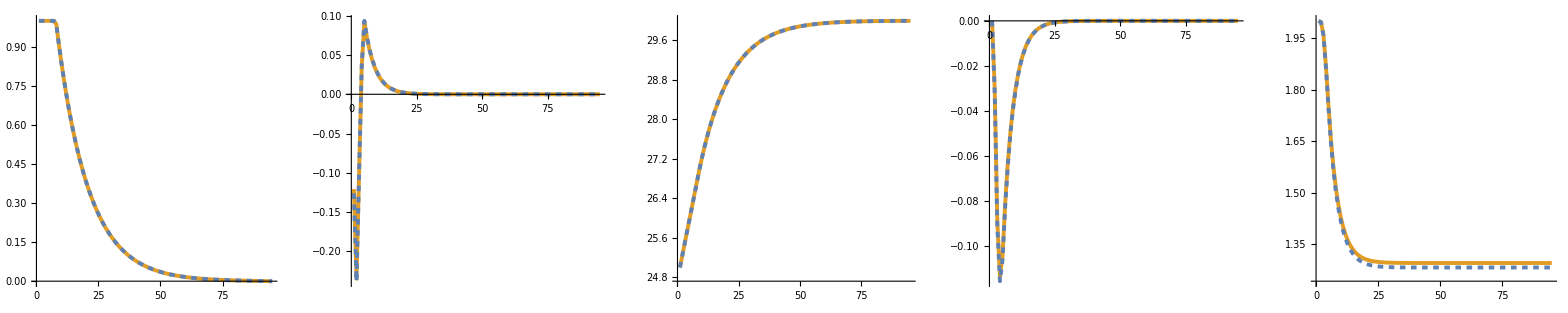

Iteration 8

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94)(ux
1.
1.
1.
1.
1.
1.
1.
0.987915
0.91284
0.84347
0.779371
0.720144
0.665417
0.614849
0.568124
0.52495
0.485057
0.448195
0.414135
0.382663
0.353582
0.326712
0.301883
0.278941
0.257743
0.238155
0.220056
0.203332
0.187879
0.173601
0.160407
0.148216
0.136951
0.126542
0.116924
0.108037
0.0998253
0.0922373
0.0852257
0.0787469
0.0727601
0.0672282
0.0621164
0.0573928
0.053028
0.0489946
0.0452674
0.0418231
0.0386402
0.0356988
0.0329805
0.0304684
0.0281466
0.0260008
0.0240175
0.0221844
0.0204898
0.0189234
0.0174751
0.0161362
0.014898
0.013753
0.012694
0.0117142
0.0108077
0.00996875
0.00919209
0.00847288
0.00780663
0.00718917
0.00661664
0.00608546
0.00559232
0.00513413
0.00470803
0.00431135
0.00394162
0.00359653
0.00327391
0.00297176
0.00268818
0.0024214
0.00216975
0.00193167
0.00170565
0.0014903
0.00128426
0.00108625
0.000895031
0.000709403
0.000528208
0.000350316
0.000174612
0.
0.)(uy
-0.123269
-0.236424
-0.0975123
0.0368576
0.0927689
0.0722952
0.05634
0.043906
0.0342161
0.0266648
0.02078
0.0161939
0.01262
0.00983483
0.00766432
0.00597284
0.00465466
0.0036274
0.00282685
0.00220298
0.00171679
0.0013379
0.00104263
0.000812528
0.000633207
0.000493461
0.000384556
0.000299686
0.000233547
0.000182004
0.000141837
0.000110534
0.0000861396
0.0000671289
0.0000523139
0.0000407684
0.000031771
0.0000247593
0.000019295
0.0000150367
0.0000117182
9.13202×10^-6
7.11663×10^-6
5.54602×10^-6
4.32204×10^-6
3.36818×10^-6
2.62484×10^-6
2.04555×10^-6
1.59411×10^-6
1.24229×10^-6
9.68125×10^-7
7.54464×10^-7
5.87957×10^-7
4.58198×10^-7
3.57075×10^-7
2.7827×10^-7
2.16857×10^-7
1.68998×10^-7
1.31701×10^-7
1.02635×10^-7
7.9984×10^-8
6.23319×10^-8
4.85755×10^-8
3.78551×10^-8
2.95006×10^-8
2.299×10^-8
1.79162×10^-8
1.39621×10^-8
1.08807×10^-8
8.47939×10^-9
6.608×10^-9
5.14961×10^-9
4.01307×10^-9
3.12734×10^-9
2.43708×10^-9
1.89913×10^-9
1.47988×10^-9
1.15312×10^-9
8.98435×10^-10
6.99899×10^-10
5.45107×10^-10
4.24383×10^-10
3.30184×10^-10
2.56621×10^-10
1.99098×10^-10
1.54017×10^-10
1.18563×10^-10
9.0519×10^-11
6.81324×10^-11
5.00041×10^-11
3.5001×10^-11
2.21855×10^-11
1.07566×10^-11
0.
0.)(x
15.
40.0313
65.3125
90.8438
116.625
142.656
168.938
195.469
222.25
249.275
276.527
303.987
331.64
359.472
387.469
415.617
443.907
472.326
500.866
529.516
558.269
587.117
616.053
645.069
674.16
703.32
732.544
761.827
791.164
820.552
849.986
879.464
908.981
938.534
968.122
997.741
1027.39
1057.06
1086.76
1116.49
1146.23
1175.99
1205.77
1235.57
1265.38
1295.21
1325.05
1354.9
1384.77
1414.64
1444.52
1474.42
1504.32
1534.22
1564.14
1594.06
1623.99
1653.92
1683.86
1713.8
1743.75
1773.7
1803.65
1833.61
1863.57
1893.54
1923.5
1953.47
1983.44
2013.42
2043.39
2073.37
2103.35
2133.33
2163.31
2193.29
2223.28
2253.26
2283.25
2313.24
2343.23
2373.21
2403.2
2433.19
2463.18
2493.18
2523.17
2553.16
2583.15
2613.14
2643.14
2673.13
2703.12
2733.11
2763.11)(y
2.
1.99615
1.95794
1.86497
1.75182
1.64963
1.57
1.50794
1.45957
1.42188
1.39251
1.36962
1.35178
1.33788
1.32705
1.31861
1.31203
1.3069
1.3029
1.29979
1.29736
1.29547
1.294
1.29285
1.29196
1.29126
1.29071
1.29029
1.28996
1.2897
1.2895
1.28935
1.28923
1.28913
1.28906
1.289
1.28895
1.28892
1.28889
1.28887
1.28885
1.28884
1.28883
1.28882
1.28882
1.28881
1.28881
1.28881
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888
1.2888)(vx
25.
25.25
25.5
25.75
26.
26.25
26.5
26.75
26.997
27.2252
27.4361
27.6309
27.8109
27.9773
28.131
28.273
28.4043
28.5255
28.6376
28.7411
28.8368
28.9252
29.0069
29.0823
29.1521
29.2165
29.276
29.3311
29.3819
29.4289
29.4723
29.5124
29.5494
29.5836
29.6153
29.6445
29.6715
29.6965
29.7195
29.7408
29.7605
29.7787
29.7955
29.8111
29.8254
29.8387
29.8509
29.8622
29.8727
29.8823
29.8913
29.8995
29.9071
29.9142
29.9207
29.9267
29.9322
29.9373
29.9421
29.9464
29.9505
29.9542
29.9576
29.9608
29.9637
29.9664
29.9689
29.9712
29.9733
29.9753
29.9771
29.9788
29.9803
29.9817
29.983
29.9841
29.9852
29.9862
29.9871
29.9879
29.9887
29.9893
29.9899
29.9905
29.991
29.9914
29.9918
29.9921
29.9924
29.9926
29.9928
29.9929
29.993
29.993
29.993)(vy
0.
-0.0308173
-0.0899233
-0.114301
-0.105087
-0.0818947
-0.0638209
-0.0497359
-0.0387594
-0.0302054
-0.0235392
-0.0183442
-0.0142957
-0.0111407
-0.00868201
-0.00676593
-0.00527272
-0.00410905
-0.0032022
-0.00249549
-0.00194475
-0.00151555
-0.00118108
-0.000920417
-0.000717285
-0.000558983
-0.000435618
-0.000339479
-0.000264558
-0.000206171
-0.00016067
-0.000125211
-0.0000975774
-0.0000760425
-0.0000592602
-0.0000461818
-0.0000359897
-0.0000280469
-0.0000218571
-0.0000170333
-0.0000132741
-0.0000103446
-8.06159×10^-6
-6.28243×10^-6
-4.89593×10^-6
-3.81542×10^-6
-2.97337×10^-6
-2.31716×10^-6
-1.80577×10^-6
-1.40725×10^-6
-1.09667×10^-6
-8.54643×10^-7
-6.66027×10^-7
-5.19038×10^-7
-4.04489×10^-7
-3.1522×10^-7
-2.45652×10^-7
-1.91438×10^-7
-1.49188×10^-7
-1.16263×10^-7
-9.06044×10^-8
-7.06084×10^-8
-5.50255×10^-8
-4.28816×10^-8
-3.34178×10^-8
-2.60427×10^-8
-2.02952×10^-8
-1.58161×10^-8
-1.23256×10^-8
-9.60541×10^-9
-7.48556×10^-9
-5.83356×10^-9
-4.54616×10^-9
-3.54289×10^-9
-2.76106×10^-9
-2.15179×10^-9
-1.677×10^-9
-1.30703×10^-9
-1.01875×10^-9
-7.94144×10^-10
-6.1917×10^-10
-4.82893×10^-10
-3.76797×10^-10
-2.94251×10^-10
-2.30096×10^-10
-1.80321×10^-10
-1.41817×10^-10
-1.12176×10^-10
-8.95464×10^-11
-7.25133×10^-11
-6.00123×10^-11
-5.1262×10^-11
-4.57156×10^-11
-4.30265×10^-11
-4.30265×10^-11)

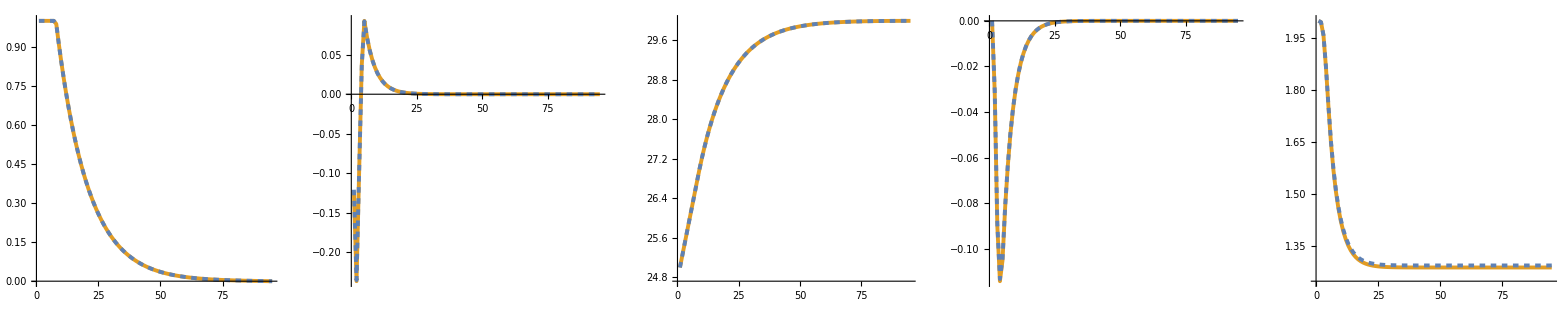

Iteration 9

$Aborted

```mathematica
Differential Dynamic Programming;
it=0;
costFullPrev=1000000;
While[True,
StringForm["Iteration ``",it+1]//Print;
alphaStore=Table[{},{i,1,K}];betaStore=Table[{},{i,1,K}];
PPStore=Table[{},{i,1,K}];QQStore=Table[{},{i,1,K}];constStore=Table[0.0,{i,1,K}];

dx1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dx+dvx*T+0.5*dax*T^2;
dy1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dy+dvy*T+0.5*day*T^2;
dvx1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dvx+dax*T;
dvy1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dvy+day*T;


(*k=K*)
xPoint=xInit[[K]];vxPoint=vxInit[[K]];axPoint=axInit[[K]];
yPoint=yInit[[K]];vyPoint=vyInit[[K]];ayPoint=ayInit[[K]];

AA=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});EE=({{0}, {0}, {0}, {0}});

PP=AA;QQ=EE;
V[dx_,dy_,dvx_,dvy_,PP_,QQ_]:=0.5*({{dx, dy, dvx, dvy}}).PP.({{dx}, {dy}, {dvx}, {dvy}})+({{dx, dy, dvx, dvy}}).QQ;
alpha=({{0}, {0}});beta=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
alphaStore[[K]]=alpha;betaStore[[K]]=beta;
PPStore[[K]]=PP;QQStore[[K]]=QQ;


(* k<=K-1 *)
For[k=K-1,k≥1,k--,
xPoint=xInit[[k]];vxPoint=vxInit[[k]];axPoint=axInit[[k]];
yPoint=yInit[[k]];vyPoint=vyInit[[k]];ayPoint=ayInit[[k]];

ayUp[ayPoint_]:=-(ayMax-ayPoint);ayLow[ayPoint_]:=ayMin-ayPoint;
axUp[axPoint_]:=-(axMax-axPoint);axLow[axPoint_]:=axMin-axPoint;
rbu[dy_,dvy_]:=-(-ayPoint-dy*Klat+dvy*(-2*Sqrt[Klat]+(Klat*T)/2)+(-2*Sqrt[Klat]+(Klat*T)/2)*vyPoint+Klat*(yMax-yPoint));
rbl[dy_,dvy_]:=(-ayPoint-dy*Klat+dvy*(-2*Sqrt[Klat]+(Klat*T)/2)+(-2*Sqrt[Klat]+(Klat*T)/2)*vyPoint+Klat*(yMin-yPoint));

axTaylor[dax_]:=0.5*dax^2+axPoint* dax+0.5*axPoint^2;
ayTaylor[day_]:=0.5*day^2+ayPoint* day+0.5*ayPoint^2;
vxTaylor[dvx_]:=0.5*dvx^2+(vxPoint-vdx)* dvx+0.5*(vxPoint-vdx)^2;
vyTaylor[dvy_]:=0.5*dvy^2+(vyPoint-vdy)* dvy+0.5*(vyPoint-vdy)^2;
ellipseTaylor[dx_,dy_,dvx_,dvy_,obsx_,obsy_]:=E^(-Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2])+(dx*obsx+dy*obsy*p-dx*xPoint-dy*p*yPoint)/(E^Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2])+(dx^2*obsx^4+2*dx*dy*obsx^3*obsy*p+dx^2*obsx^2*obsy^2*p+dy^2*obsx^2*obsy^2*p^2+2*dx*dy*obsx*obsy^3*p^2+dy^2*obsy^4*p^3-4*dx^2*obsx^3*xPoint-6*dx*dy*obsx^2*obsy*p*xPoint-2*dx^2*obsx*obsy^2*p*xPoint-2*dy^2*obsx*obsy^2*p^2*xPoint-2*dx*dy*obsy^3*p^2*xPoint+6*dx^2*obsx^2*xPoint^2+6*dx*dy*obsx*obsy*p*xPoint^2+dx^2*obsy^2*p*xPoint^2+dy^2*obsy^2*p^2*xPoint^2-4*dx^2*obsx*xPoint^3-2*dx*dy*obsy*p*xPoint^3+dx^2*xPoint^4-2*dx*dy*obsx^3*p*yPoint-2*dx^2*obsx^2*obsy*p*yPoint-2*dy^2*obsx^2*obsy*p^2*yPoint-6*dx*dy*obsx*obsy^2*p^2*yPoint-4*dy^2*obsy^3*p^3*yPoint+6*dx*dy*obsx^2*p*xPoint*yPoint+4*dx^2*obsx*obsy*p*xPoint*yPoint+4*dy^2*obsx*obsy*p^2*xPoint*yPoint+6*dx*dy*obsy^2*p^2*xPoint*yPoint-6*dx*dy*obsx*p*xPoint^2*yPoint-2*dx^2*obsy*p*xPoint^2*yPoint-2*dy^2*obsy*p^2*xPoint^2*yPoint+2*dx*dy*p*xPoint^3*yPoint+dx^2*obsx^2*p*yPoint^2+dy^2*obsx^2*p^2*yPoint^2+6*dx*dy*obsx*obsy*p^2*yPoint^2+6*dy^2*obsy^2*p^3*yPoint^2-2*dx^2*obsx*p*xPoint*yPoint^2-2*dy^2*obsx*p^2*xPoint*yPoint^2-6*dx*dy*obsy*p^2*xPoint*yPoint^2+dx^2*p*xPoint^2*yPoint^2+dy^2*p^2*xPoint^2*yPoint^2-2*dx*dy*obsx*p^2*yPoint^3-4*dy^2*obsy*p^3*yPoint^3+2*dx*dy*p^2*xPoint*yPoint^3+dy^2*p^3*yPoint^4-dy^2*obsx^2*p*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dx*dy*obsx*obsy*p*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-dx^2*obsy^2*p*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dy^2*obsx*p*xPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-2*dx*dy*obsy*p*xPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-dy^2*p*xPoint^2*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-2*dx*dy*obsx*p*yPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dx^2*obsy*p*yPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dx*dy*p*xPoint*yPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-dx^2*p*yPoint^2*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2])/(2*E^Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]*(obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2)^2);

L[dx_,dy_,dvx_,dvy_,dax_,day_,PP_,QQ_]:=w1*axTaylor[dax]+w2*ayTaylor[day]+w3*vxTaylor[dvx]+w4*vyTaylor[dvy]+w5*Sum[ellipseTaylor[dx,dy,dvx,dvy,xObs[[i,k]],yObs[[i,k]]],{i,1,numObs}]
+V[dx1[dx,dy,dvx,dvy,dax,day],dy1[dx,dy,dvx,dvy,dax,day],dvx1[dx,dy,dvx,dvy,dax,day],dvy1[dx,dy,dvx,dvy,dax,day],PP,QQ][[1,1]];

(*x^T.B.x*)
dxdx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dx,2}];dxdy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx,dy];
dxdvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx,dvx];dxdvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx,dvy];
dydx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy,dx];dydy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dy,2}];
dydvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy,dvx];dydvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy,dvy];
dvxdx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx,dx];dvxdy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx,dy];
dvxdvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dvx,2}];dvxdvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx,dvy];
dvydx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy,dx];dvydy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy,dy];
dvydvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy,dvx];dvydvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dvy,2}];
AA=({{dxdx, dxdy, dxdvx, dxdvy}, {dydx, dydy, dydvx, dydvy}, {dvxdx, dvxdy, dvxdvx, dvxdvy}, {dvydx, dvydy, dvydvx, dvydvy}});

(*a^T.B.x*)
xaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx dax];yaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy dax];
vxaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx dax];vyaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy dax];
xayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx day];yayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy day];
vxayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx day];vyayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy day];
BB=({{xaxCoeff, xayCoeff}, {yaxCoeff, yayCoeff}, {vxaxCoeff, vxayCoeff}, {vyaxCoeff, vyayCoeff}});

(*a^T.B.a*)
daxdax=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dax,2}];dayday=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{day,2}];
CC=({{daxdax, 0}, {0, dayday}});
(*a^T.D*)
axcl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dax],{dax,day,dx,dy,dvx,dvy}];
aycl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],day],{dax,day,dx,dy,dvx,dvy}];
If[axcl=={},axCoeff=0.0,axCoeff=axcl[[1,1,1,1,1,1]]];If[aycl=={},ayCoeff=0.0,ayCoeff=aycl[[1,1,1,1,1,1]]];

DD=({{axCoeff}, {ayCoeff}});
(*x^T.E*)
xcl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx],{dax,day,dx,dy,dvx,dvy}];
ycl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy],{dax,day,dx,dy,dvx,dvy}];
vxcl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx],{dax,day,dx,dy,dvx,dvy}];
vycl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy],{dax,day,dx,dy,dvx,dvy}];
If[xcl=={},xCoeff=0.0,xCoeff=xcl[[1,1,1,1,1,1]]];If[ycl=={},yCoeff=0.0,yCoeff=ycl[[1,1,1,1,1,1]]];
If[vxcl=={},vxCoeff=0.0,vxCoeff=vxcl[[1,1,1,1,1,1]]];If[vycl=={},vyCoeff=0.0,vyCoeff=vycl[[1,1,1,1,1,1]]];

EE=({{xCoeff}, {yCoeff}, {vxCoeff}, {vyCoeff}});

(*Constrained DDP*)
qq=-DD-Transpose[BB].({{xPoint}, {yPoint}, {vxPoint}, {vyPoint}});
Ct={};d={};R={};
While[True,
(* Active Constraints *)
(*ax bounds*)
If[axUp[axPoint]>=0.0,
AppendTo[Ct,{-1,0}];AppendTo[d,{axUp[axPoint]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (axMax)",k]];
If[axMin>=axPoint,
AppendTo[Ct,{1,0}];AppendTo[d,{axLow[axPoint]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (axMin)",k]];
(*ay bounds*)
(*If[ayUp>=0.0,
AppendTo[Ct,{0,-1}];AppendTo[d,{ayUp}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (ayMax)",k]//Print];*)
(*If[ayMin>=ayPoint,
AppendTo[Ct,{0,1}];AppendTo[d,{ayLow}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (ayMin)",k]//Print];*)
(*road bounds*)
(*If[rbu[0.0,0.0]>=0.0,
AppendTo[Ct,{0,-1}];AppendTo[d,{rbu[0.0,0.0]}];AppendTo[R,{D[rbu[dy,dvy],dx],D[rbu[dy,dvy],dy],D[rbu[dy,dvy],dvx],D[rbu[dy,dvy],dvy]}];
StringForm["(``) Constraint Activation (rbUp)",k]//Print];
If[rbl[0.0,0.0]>=0.0,
AppendTo[Ct,{0,1}];AppendTo[d,{rbl[0.0,0.0]}];AppendTo[R,{D[rbl[dy,dvy],dx],D[rbl[dy,dvy],dy],D[rbl[dy,dvy],dvx],D[rbl[dy,dvy],dvy]}];
StringForm["(``) Constraint Activation (rbUp)",k]//Print];*)

If[d=={},Ct={{0,0}};d={{0}};R={{0,0,0,0}}];

(* Quadratic Problem for Active Constraints *)
tempCstar=Ct.Inverse[CC].Transpose[Ct];(*(4x2).(2x2).(2x4)->(4x4)*)
If[Det[tempCstar]!=0,tempCstar=Inverse[tempCstar]];
Cstar=tempCstar.Ct.Inverse[CC];(*(4x4).(4x2).(2x2)->(4x2)*)

Hstar=Inverse[CC].(({{1.0, 0.0}, {0.0, 1.0}})-Transpose[Ct].Cstar);(*(2x2).[(2x2)-(2x4).(4x2)]->(2x2)*)
(*Hstar=Inverse[CC]-(Inverse[CC].Transpose[Ct].Cstar);(*(2x2).[(2x2)-(2x4).(4x2)]->(2x2)*)*)

pStar=-Hstar.qq+Transpose[Cstar].d;(*(2x2).(2x1)+(2x4).(4x1)->(2x1)*)
lambdaStar=Cstar.qq-tempCstar.d;(*(4x2).(2x1)-(4x4).(4x1)->(4x1)*)

(*If[axLow[axPoint]>pStar[[1,1]],
Ct={};d={};R={};
error=pStar[[1,1]]-axPoint;
AppendTo[Ct,{1,0}];AppendTo[d,{axLow[pStar[[1,1]]]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) pStar: `` | axPoint: `` | c[axPoint]: `` | c[pStar]: ``",k,pStar[[1,1]],axPoint,axLow[axPoint],axLow[pStar[[1,1]]]]//Print;

tempCstar=Ct.Inverse[CC].Transpose[Ct];(*(4x2).(2x2).(2x4)->(4x4)*)
If[Det[tempCstar]!=0,tempCstar=Inverse[tempCstar]];
Cstar=tempCstar.Ct.Inverse[CC];(*(4x4).(4x2).(2x2)->(4x2)*)
Hstar=Inverse[CC]-(Inverse[CC].Transpose[Ct].Cstar);(*(2x2).[(2x2)-(2x4).(4x2)]->(2x2)*)
];*)

P=d;

Break[];
];

(*(2x2).(2x1)+(2x4).(4x1)->(2x1)*)
alpha=-Hstar.DD+Transpose[Cstar].P;
(*(2x2).(2x4)+(2x4).(4x4)->(2x4)*)
beta=-Hstar.Transpose[BB]+Transpose[Cstar].R;
(*MatrixForm[alpha]//Print;*)
PP=AA+Transpose[beta].CC.beta+BB.beta+Transpose[beta].Transpose[BB];
QQ=EE+Transpose[beta].CC.alpha+BB.alpha+Transpose[beta].DD;

alphaStore[[k]]=alpha;betaStore[[k]]=beta;
PPStore[[k]]=PP;QQStore[[k]]=QQ;
];

(* Forward Pass *)
While[True,
axInitNext={};vxInitNext={};xInitNext={};
ayInitNext={};vyInitNext={};yInitNext={};

xDDP=xInit[[1]];vxDDP=vxInit[[1]];
yDDP=yInit[[1]];vyDDP=vyInit[[1]];

vxInitNext=AppendTo[vxInitNext,vxDDP];
vyInitNext=AppendTo[vyInitNext,vyDDP];
xInitNext=AppendTo[xInitNext,xDDP];
yInitNext=AppendTo[yInitNext,yDDP];
costFull=0.0;

For[k=1,k<K,k++,
dxDDP=(xDDP-xInit[[k]]);dvxDDP=(vxDDP-vxInit[[k]]);
dyDDP=(yDDP-yInit[[k]]);dvyDDP=(vyDDP-vyInit[[k]]);

uDDP=({{axInit[[k]]}, {ayInit[[k]]}})+eps*(alphaStore[[k]])+betaStore[[k]].({{dxDDP}, {dyDDP}, {dvxDDP}, {dvyDDP}});
uxDDP=uDDP[[1,1]];uyDDP=uDDP[[2,1]];

xDDP=xDDP+vxDDP+0.5*uxDDP*T^2;
yDDP=yDDP+vyDDP+0.5*uyDDP*T^2;
vxDDP=vxDDP+uxDDP*T;
vyDDP=vyDDP+uyDDP*T;

axInitNext=AppendTo[axInitNext,uxDDP];ayInitNext=AppendTo[ayInitNext,uyDDP];
vxInitNext=AppendTo[vxInitNext,vxDDP];vyInitNext=AppendTo[vyInitNext,vyDDP];
xInitNext=AppendTo[xInitNext,xDDP];yInitNext=AppendTo[yInitNext,yDDP];
];

Break[];
];
AppendTo[axInitNext,0.0];AppendTo[ayInitNext,0.0];
timeSteps=Table[i,{i,0,K-1}];
axPrt=axInitNext;ayPrt=ayInitNext;xPrt=xInitNext;yPrt=yInitNext;vxPrt=vxInitNext;vyPrt=vyInitNext;
Print[MatrixForm[PrependTo[timeSteps,"k"]],MatrixForm[PrependTo[axPrt,"ux"]],MatrixForm[PrependTo[ayPrt,"uy"]],MatrixForm[PrependTo[xPrt,"x"]],MatrixForm[PrependTo[yPrt,"y"]],MatrixForm[PrependTo[vxPrt,"vx"]],MatrixForm[PrependTo[vyPrt,"vy"]]];

(*Plots*)
myPlot[K,15];

If[((Norm[axInitNext-axInit]< epsilon && Norm[ayInitNext-ayInit]< epsilon) || it>=maxIter),
Print["Terminal criterion met |ax - axPrev|: ", Norm[axInitNext-axInit]];
Print["Terminal criterion met |ay - ayPrev|: ", Norm[ayInitNext-ayInit]];
simOutput[K,T];
Break[];
];

axInit=axInitNext;vxInit=vxInitNext;xInit=xInitNext;
ayInit=ayInitNext;vyInit=vyInitNext;yInit=yInitNext;
it=it+1;
]
```